```mathematica
<<"~/git_synchros/DoFun/DoFun/Kernel/init.m"
$signConvention=1;
```

DoFun loaded.

Version 3.2.0
Reinhard Alkofer, Jens Braun, Anton K. Cyrol, Markus Q. Huber, Jan M. Pawlowski, Kai Schwenzer, 2008-2019

Details at https://github.com/markusqh/DoFun/.

```mathematica
<<"~/git_synchros/DoFun/DoFun/DoDSERGE.m"
```

```mathematica
Labeled["G", Style[Row[{Overscript[Style["",FontSize:>50],Style["",(factorStyle/.Options@DSEPlot)
   			/.(FontSize:>w_Integer):>(FontSize:>w)]],DisplayForm@AdjustmentBox["=",BoxBaselineShift->-1.6]}],
   		ShowStringCharacters->False,factorStyle/.Options@DSEPlot],Right]
```

G^=

```mathematica
AdjustmentBox["=",BoxMargins->1]//DisplayForm
```

=

# Examples

## phi^3-phi^4 theory (3PI)

### Definitions

```mathematica
setFields[{phi}];
```

```mathematica
fieldStyles={{phi,Black}};
```

```mathematica
action3PI=(* eight *)1/8op[S[{phi,i1},{phi,i2},{phi,i3},{phi,i4}],P[{phi,i1},{phi,i2}],P[{phi,i3},{phi,i4}]]+(* sunset SV *)1/6op[S[{phi,i1},{phi,i2},{phi,i3}],P[{phi,i1},{phi,i1s}],P[{phi,i3},{phi,i3s}],P[{phi,i2},{phi,i2s}],V[{phi,i1s},{phi,i2s},{phi,i3s}]]+(* eye *)1/48op[S[{phi,i1},{phi,i2},{phi,i3},{phi,i4}],P[{phi,i1},{phi,i1s}],P[{phi,i3},{phi,i3s}],P[{phi,i2},{phi,i2s}],P[{phi,i4},{phi,i4s}],S[{phi,i1s},{phi,i2s},{phi,i3s},{phi,i4s}]]+(* double squint *)1/8op[S[{phi,i1},{phi,i2},{phi,i3},{phi,i4}],P[{phi,i1},{phi,i1s}],P[{phi,i3},{phi,i3s}],P[{phi,i2},{phi,i2s}],P[{phi,i4},{phi,i4s}],P[{phi,i5},{phi,i5s}],V[{phi,i1s},{phi,i2s},{phi,i5}],V[{phi,i3s},{phi,i4s},{phi,i5s}]]-(* sunset VV *)1/12op[V[{phi,i1},{phi,i2},{phi,i3}],P[{phi,i1},{phi,i1s}],P[{phi,i3},{phi,i3s}],P[{phi,i2},{phi,i2s}],V[{phi,i1s},{phi,i2s},{phi,i3s}]]+(* star *)1/24op[V[{phi,i1},{phi,i2},{phi,i3}],P[{phi,i1},{phi,i1s}],P[{phi,i3},{phi,i3s}],P[{phi,i2},{phi,i2s}],V[{phi,i1s},{phi,i4},{phi,i5}],P[{phi,i4},{phi,i4s}],P[{phi,i5},{phi,i5s}],V[{phi,i2s},{phi,i4s},{phi,i6}],P[{phi,i6},{phi,i6s}],V[{phi,i3s},{phi,i5s},{phi,i6s}]];
```

Action:

```mathematica
DSEPlot[action3PI,fieldStyles]
```

DSEPlot::noDerivs: The expression seems to be a vacuum graph (external fields are {}). Use NPIPlot instead of DSEPlot.

$Aborted

```mathematica
NPIPlot[action3PI,fieldStyles]
```

Γ^= | -Graphics-+1/8^-1 | -Graphics-+1/6^ | -Graphics--1/12^ | -Graphics-+1/48^
 | -Graphics-+1/8^ | -Graphics-+1/24^ |  |

### Vertex

```mathematica
eomVertDiagsPre=diffV[action3PI,V[{phi,i},{phi,j},{phi,k}]];
eomVertDiagsPreId=identifyGraphs[clipExtProps@eomVertDiagsPre,{{phi,i},{phi,j},{phi,k}}];
```

```mathematica
DSEPlot[eomVertDiagsPreId,fieldStyles,output->List]
```

{-Graphics-+1/6^,-Graphics--1/6^,-Graphics-+1/12^,-Graphics-+1/12^,-Graphics-+1/12^,-Graphics-+1/6^}

Select diagrams:

```mathematica
eomVert=6eomVertDiagsPreId[[{1,3,4,5,6}]];
```

```mathematica
DSEPlot[eomVert,fieldStyles]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+^ |  |  |

### Propagator

```mathematica
eomPropPre=identifyGraphs[op[S[{phi,i},{phi,j}]]-2diffP[action3PI,P[{phi,i},{phi,j}]]//Expand,{{phi,i},{phi,j}}];
```

```mathematica
DSEPlot[eomPropPre,fieldStyles,output->List]
```

{-Graphics-+^-1,-Graphics--1/2^,-Graphics--1/2^,-Graphics-+1/2^,-Graphics--1/2^,-Graphics--1/6^,-Graphics--1/2^,-Graphics--1/4^,-Graphics--1/2^,-Graphics--1/2^}

Put in vertex eom (derivation elsewhere):

```mathematica
DSEPlot[eomVert,fieldStyles]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+^ |  |  |

Manual replacement of vertex.

```mathematica
Clear[dummyRules]
dummyRules[a_ exp_op,rest___]:=dummyRules[exp,rest]
dummyRules[exp_op,extFields_List]:=Module[{intInds,dummies},
intInds=Union@DeleteCases[Cases[exp,{phi,i_}:>i,∞],Alternatives@@extFields[[All,2]]];

Thread@Rule[intInds,Table[insDummy[],{Length@intInds}]]
]
```

```mathematica
Clear@vertRepls
vertRepls[i_,j_,k_]=Expand[eomVert/.a_op:>(a/.dummyRules[a,{{phi,i},{phi,j},{phi,k}}])];
```

```mathematica
DSEPlot[eomPropPre,fieldStyles,output->List]
```

{-Graphics-+^-1,-Graphics--1/2^,-Graphics--1/2^,-Graphics-+1/2^,-Graphics--1/2^,-Graphics--1/6^,-Graphics--1/2^,-Graphics--1/4^,-Graphics--1/2^,-Graphics--1/2^}

Show results of replacement of the dressed vertex in the appropriate diagram:

```mathematica
DSEPlot[eomPropPre[[4]],fieldStyles]
DSEPlot[eomPropPre[[4]]/.V[{phi,i},{phi,i1_},{phi,i2_}]:>vertRepls[i,i1,i2]//Expand,fieldStyles,output->List]
```

-Graphics-+1/2^

{-Graphics-+1/2^,-Graphics-+1/4^,-Graphics-+1/4^,-Graphics-+1/4^,-Graphics-+1/2^}

Perform manual replacement of the vertex in one diagram:

```mathematica
eomPropPre2=eomPropPre[[{1,2,3,5,6,7,8,9,10}]]+(eomPropPre[[4]]/.V[{phi,i},{phi,i1_},{phi,i2_}]:>vertRepls[i,i1,i2]);
DSEPlot[eomPropPre2,fieldStyles]
eomProp=identifyGraphs[eomPropPre2,{{phi,i},{phi,j}}];
DSEPlot[eomProp,fieldStyles]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/6^
 | -Graphics--1/2^ | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics--1/4^
 | -Graphics--1/2^ | -Graphics-+1/4^ | -Graphics--1/2^ | -Graphics-+1/2^

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/6^
 | -Graphics--1/2^ |  |  |

## Fermionic example (YM, 3PI)

### Definitions

```mathematica
setFields[{A},{{c,cb},{psi,psib}}];
```

```mathematica
fieldStyles={{A,Red},{psi,Blue},{c,Green}};
```

```mathematica
actionYM3PI=(* eight *)1/8op[S[{A,i1},{A,i2},{A,i3},{A,i4}],P[{A,i1},{A,i2}],P[{A,i3},{A,i4}]]+(* sunset SV gluon *)1/6op[S[{A,i1},{A,i2},{A,i3}],P[{A,i1},{A,i1s}],P[{A,i3},{A,i3s}],P[{A,i2},{A,i2s}],V[{A,i1s},{A,i2s},{A,i3s}]]-(* sunset SV ghost-gluon*)op[S[{A,i1},{cb,i2},{c,i3}],P[{A,i1},{A,i1s}],P[{c,i3},{cb,i3s}],P[{c,i2s},{cb,i2}],V[{A,i1s},{cb,i3s},{c,i2s}]]+(* eye *)1/48op[S[{A,i1},{A,i2},{A,i3},{A,i4}],P[{A,i1},{A,i1s}],P[{A,i3},{A,i3s}],P[{A,i2},{A,i2s}],P[{A,i4},{A,i4s}],S[{A,i1s},{A,i2s},{A,i3s},{A,i4s}]]+(* double squint *)1/8op[S[{A,i1},{A,i2},{A,i3},{A,i4}],P[{A,i1},{A,i1s}],P[{A,i3},{A,i3s}],P[{A,i2},{A,i2s}],P[{A,i4},{A,i4s}],P[{A,i5},{A,i5s}],V[{A,i1s},{A,i2s},{A,i5}],V[{A,i3s},{A,i4s},{A,i5s}]]-(* sunset VV gluon *)1/12op[V[{A,i1},{A,i2},{A,i3}],P[{A,i1},{A,i1s}],P[{A,i3},{A,i3s}],P[{A,i2},{A,i2s}],V[{A,i1s},{A,i2s},{A,i3s}]]+(* sunset VV ghost-gluon*)1/2op[V[{A,i1},{cb,i2},{c,i3}],P[{A,i1},{A,i1s}],P[{c,i3},{cb,i3s}],P[{c,i2s},{cb,i2}],V[{A,i1s},{cb,i3s},{c,i2s}]]+(* star gluon *)1/24op[V[{A,i1},{A,i2},{A,i3}],P[{A,i1},{A,i1s}],P[{A,i3},{A,i3s}],P[{A,i2},{A,i2s}],V[{A,i1s},{A,i4},{A,i5}],P[{A,i4},{A,i4s}],P[{A,i5},{A,i5s}],V[{A,i2s},{A,i4s},{A,i6}],P[{A,i6},{A,i6s}],V[{A,i3s},{A,i5s},{A,i6s}]]-(* star ghost-gluon Abelian *)1/4op[V[{A,i1},{cb,i5},{c,i8s}],
V[{A,i2},{cb,i6},{c,i5s}],
V[{A,i3},{cb,i7},{c,i6s}],
V[{A,i4},{cb,i8},{c,i7s}],
P[{A,i1},{A,i3}],P[{A,i2},{A,i4}],
P[{c,i5s},{cb,i5}],P[{c,i6s},{cb,i6}],P[{c,i7s},{cb,i7}],P[{c,i8s},{cb,i8}]]-(* star ghost-gluon non-Abelian *)1/3op[V[{A,i1},{A,i2},{A,i3}],
V[{A,i1s},{cb,i4},{c,i5s}],
V[{A,i2s},{cb,i5},{c,i6s}],
V[{A,i3s},{cb,i6},{c,i4s}],
P[{A,i1},{A,i1s}],P[{A,i2},{A,i2s}],P[{A,i3},{A,i3s}],
P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]];
```

```mathematica
DSEPlot[actionYM3PI,fieldStyles]
```

Γ^k^= | -Graphics-+1/8^-1 | -Graphics-+1/6^ | -Graphics--^ | -Graphics--1/12^
 | -Graphics-+1/2^ | -Graphics-+1/48^ | -Graphics-+1/8^ | -Graphics-+1/24^
 | -Graphics--1/3^ | -Graphics--1/4^ |  |

### Vertices

#### AAA

```mathematica
eomAAADiagsPre=diffV[actionYM3PI,V[{A,i},{A,j},{A,k}]];
eomAAADiagsPreId=identifyGraphs[clipExtProps@eomAAADiagsPre,{{A,i},{A,j},{A,k}}];
```

```mathematica
DSEPlot[eomAAADiagsPreId,fieldStyles,output->List]
```

{-Graphics-+1/6^,-Graphics--1/6^,-Graphics-+1/12^,-Graphics-+1/12^,-Graphics-+1/12^,-Graphics-+1/6^,-Graphics--1/3^}

Select diagrams:

```mathematica
eomAAA=6eomAAADiagsPreId[[{1,3,4,5,6,7}]]//Expand;
```

```mathematica
DSEPlot[eomAAA,fieldStyles]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+^ | -Graphics--2^ |  |

#### Acbc

```mathematica
eomAcbcDiagsPre=diffV[actionYM3PI,V[{A,i},{cb,k},{c,j}]];
eomAcbcDiagsPreId=identifyGraphs[clipExtProps@eomAcbcDiagsPre,{{A,i},{cb,j},{c,k}}];
```

Note: The derivative with respect to V[{A, i}, {cb, j}, {c, k}] yields as external legs {{A, i}, {c, j}, {c, k}}!

```mathematica
eomAcbcDiagsPre=diffV[actionYM3PI,V[{A,i},{cb,k},{c,j}]];
eomAcbcDiagsPreId=identifyGraphs[clipExtProps@eomAcbcDiagsPre,{{A,i},{antiField@cb,k},{antiField@c,j}}];
```

```mathematica
eomAcbcDiagsPreId[[3]]
```

-op[V[{A,i},{A,i1},{A,i3}],V[{A,i1s},{cb,i4},{c,k}],V[{A,i3s},{cb,j},{c,i4s}],P[{A,i1},{A,i1s}],P[{A,i3},{A,i3s}],P[{c,i4s},{cb,i4}]]

```mathematica
DSEPlot[eomAcbcDiagsPreId,fieldStyles,output->List]
```

{-Graphics--^,-Graphics-+^,-Graphics--^,-Graphics--^}

Select diagrams:

```mathematica
eomAcbc=-eomAcbcDiagsPreId[[{1,3,4}]]//Expand
```

op[S[{A,i},{cb,j},{c,k}]]+op[V[{A,i},{A,i1},{A,i3}],V[{A,i1s},{cb,i4},{c,k}],V[{A,i3s},{cb,j},{c,i4s}],P[{A,i1},{A,i1s}],P[{A,i3},{A,i3s}],P[{c,i4s},{cb,i4}]]+op[V[{A,i},{cb,i5},{c,i8s}],V[{A,i4},{cb,i8},{c,k}],V[{A,i2},{cb,j},{c,i5s}],P[{A,i2},{A,i4}],P[{c,i5s},{cb,i5}],P[{c,i8s},{cb,i8}]]

```mathematica
DSEPlot[eomAcbc,fieldStyles]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ |

### Propagators

#### AA

```mathematica
eomAAPre=identifyGraphs[op[S[{A,i},{A,j}]]-2diffP[actionYM3PI,P[{A,i},{A,j}]]//Expand,{{A,i},{A,j}}];
```

```mathematica
DSEPlot[eomAAPre,fieldStyles,output->List]
```

{-Graphics-+^-1,-Graphics--1/2^,-Graphics--1/2^,-Graphics-+^,-Graphics-+1/2^,-Graphics--1/2^,-Graphics--^,-Graphics-+^,-Graphics--1/6^,-Graphics--1/2^,-Graphics--1/4^,-Graphics--1/2^,-Graphics--1/2^,-Graphics-+^,-Graphics-+^,-Graphics-+^}

Put in vertex eoms (derivations elsewhere):

```mathematica
DSEPlot[eomAAA,fieldStyles]
DSEPlot[eomAcbc,fieldStyles]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+^ | -Graphics--2^ |  |

-Graphics-^= | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ |

Manual replacement of vertex.

```mathematica
Clear[dummyRules]
dummyRules[a_ exp_op,rest___]:=dummyRules[exp,rest]
dummyRules[exp_op,extFields_List]:=Module[{intInds,dummies},
intInds=Union@DeleteCases[Cases[exp,{A|cb|c,i_}:>i,∞],Alternatives@@extFields[[All,2]]];

Thread@Rule[intInds,Table[insDummy[],{Length@intInds}]]
]
```

```mathematica
Clear@vertReplsAAA
vertReplsAAA[i_,j_,k_]=Expand[eomAAA/.a_op:>(a/.dummyRules[a,{{A,i},{A,j},{A,k}}])];
```

```mathematica
Clear@vertReplsAcbc
vertReplsAcbc[i_,j_,k_]=Expand[eomAcbc/.a_op:>(a/.dummyRules[a,{{A,i},{cb,j},{c,k}}])];
```

```mathematica
DSEPlot[eomAAPre,fieldStyles,output->List]
```

{-Graphics-+^-1,-Graphics--1/2^,-Graphics--1/2^,-Graphics-+^,-Graphics-+1/2^,-Graphics--1/2^,-Graphics--^,-Graphics-+^,-Graphics--1/6^,-Graphics--1/2^,-Graphics--1/4^,-Graphics--1/2^,-Graphics--1/2^,-Graphics-+^,-Graphics-+^,-Graphics-+^}

Show results of replacement of the dressed vertex in the third diagram:

```mathematica
DSEPlot[eomAAPre[[5]],fieldStyles]
DSEPlot[eomAAPre[[5]]/.V[{A,i},{A,i1_},{A,i2_}]:>vertReplsAAA[i,i1,i2]//Expand,fieldStyles,output->List]
```

-Graphics-+1/2^

{-Graphics-+1/2^,-Graphics-+1/4^,-Graphics-+1/4^,-Graphics-+1/4^,-Graphics-+1/2^,-Graphics--^}

```mathematica
DSEPlot[eomAAPre[[7]],fieldStyles]
DSEPlot[eomAAPre[[7]]/.V[{A,i},{cb,i1_},{c,i2_}]:>vertReplsAcbc[i,i1,i2]//Expand,fieldStyles,output->List]
```

-Graphics--^

{-Graphics--^,-Graphics--^,-Graphics--^}

Perform manual replacement of the vertex in one diagram:

```mathematica
eomAAPre2=eomAAPre[[{1,2,3,4,6,8,9,10,11,12,13,14,15,16}]]+(eomAAPre[[5]]/.V[{A,i},{A,i1_},{A,i2_}]:>vertReplsAAA[i,i1,i2])+(eomAAPre[[7]]/.V[{A,i},{cb,i1_},{c,i2_}]:>vertReplsAcbc[i,i1,i2]);
DSEPlot[eomAAPre2,fieldStyles]
eomAA=identifyGraphs[eomAAPre2,{{A,i},{A,j}}];
DSEPlot[eomAA,fieldStyles]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--1/6^ | -Graphics--1/2^ | -Graphics-+1/4^ | -Graphics-+1/4^
 | -Graphics--1/4^ | -Graphics--1/2^ | -Graphics-+1/4^ | -Graphics--1/2^
 | -Graphics-+^ | -Graphics-+1/2^ | -Graphics--^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics--^ |

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--1/6^ | -Graphics--1/2^ |  |

```mathematica
eomAAPre2=eomAAPre[[{1,2,3,4,6,8,9,10,11,12,13,14,15,16}]]+(eomAAPre[[5]]/.V[{A,j},{A,i1_},{A,i2_}]:>vertReplsAAA[j,i1,i2])+(eomAAPre[[7]]/.V[{A,j},{cb,i1_},{c,i2_}]:>vertReplsAcbc[j,i1,i2]);
DSEPlot[eomAAPre2,fieldStyles]
eomAA=identifyGraphs[eomAAPre2,{{A,i},{A,j}}];
DSEPlot[eomAA,fieldStyles]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics-+1/2^ | -Graphics--1/2^ | -Graphics--^ | -Graphics-+^
 | -Graphics--1/6^ | -Graphics--1/2^ | -Graphics-+1/4^ | -Graphics-+1/4^
 | -Graphics-+1/4^ | -Graphics--1/4^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics-+1/2^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ |

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--1/6^ | -Graphics--1/2^ |  |

#### cbc

Note the different prefactor in front of the derivative due to fermions (+1 instead of -2).

```mathematica
eomcbcPre=identifyGraphs[op[S[{cb,i},{c,j}]]+diffP[actionYM3PI,P[{c,i},{cb,j}]]//Expand,{{cb,j},{c,i}}];
```

```mathematica
DSEPlot[eomcbcPre,fieldStyles,output->List]
```

{-Graphics-+^-1,-Graphics--^,-Graphics-+^,-Graphics--^,-Graphics--^,-Graphics--^}

Put in vertex eom (derivation elsewhere):

```mathematica
DSEPlot[eomAcbc,fieldStyles]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ |

Manual replacement of vertex.

```mathematica
Clear[dummyRules]
dummyRules[a_ exp_op,rest___]:=dummyRules[exp,rest]
dummyRules[exp_op,extFields_List]:=Module[{intInds,dummies},
intInds=Union@DeleteCases[Cases[exp,{A|cb|c,i_}:>i,∞],Alternatives@@extFields[[All,2]]];

Thread@Rule[intInds,Table[insDummy[],{Length@intInds}]]
]
```

```mathematica
Clear@vertReplsAcbc
vertReplsAcbc[i_,j_,k_]=Expand[eomAcbc/.a_op:>(a/.dummyRules[a,{{A,i},{cb,j},{c,k}}])];
```

```mathematica
DSEPlot[eomcbcPre,fieldStyles,output->List]
```

{-Graphics-+^-1,-Graphics--^,-Graphics-+^,-Graphics--^,-Graphics--^,-Graphics--^}

Show results of replacement of the dressed vertex in the third diagram:

```mathematica
DSEPlot[eomcbcPre[[3]],fieldStyles]
DSEPlot[eomcbcPre[[3]]/.V[{A,i1_},{cb,i2_},{c,i}]:>vertReplsAcbc[i1,i2,i]//Expand,fieldStyles,output->List]
```

-Graphics-+^

{-Graphics-+^,-Graphics-+^,-Graphics-+^}

Perform manual replacement of the vertex in one diagram:

```mathematica
eomcbcPre2=eomcbcPre[[{1,2,4,5,6}]]+(eomcbcPre[[3]]/.V[{A,i1_},{cb,i2_},{c,i}]:>vertReplsAcbc[i1,i2,i]);
DSEPlot[eomcbcPre2,fieldStyles]
eomcbc=identifyGraphs[eomcbcPre2,{{c,i},{cb,j}}];
DSEPlot[eomcbc,fieldStyles]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ | -Graphics-+^ | -Graphics--^ | -Graphics--^

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--^ |  |

### Kernels

```mathematica
DSEPlot[actionYM3PI,fieldStyles]
```

Γ^k^= | -Graphics-+1/8^-1 | -Graphics-+1/6^ | -Graphics--^ | -Graphics--1/12^
 | -Graphics-+1/2^ | -Graphics-+1/48^ | -Graphics-+1/8^ | -Graphics-+1/24^
 | -Graphics--1/3^ | -Graphics--1/4^ |  |

#### Overview of kernels

-Graphics-^= | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+1/2^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ |  |  |

Glueball paper 1: -2,-2,-2, so difference in symmetry factors (here -2, -1, -1).

-Graphics-^= | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^

Glueball paper 1: 1,1,1, so difference in symmetry factors (here 1, 1/2, 1/2).

-Graphics-^= | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^

-Graphics-^= | -Graphics-+^ | -Graphics-+^ |  |

#### GlGl (Ghost triangles not automatically identified yet)

Correct, but ghost triangles are not identified yet. They cancel.

```mathematica
kerGlGlDer1=identifyGraphs[2diffP[actionYM3PI,P[{A,i},{A,j}]]//Expand,{{A,i},{A,j}}];
DSEPlot[kerGlGlDer1,fieldStyles]
kerGlGlDer2=identifyGraphs[diffP[kerGlGlDer1,P[{A,k},{A,l}]],{{A,i},{A,j},{A,k},{A,l}}];
DSEPlot[kerGlGlDer2,fieldStyles]
```

-Graphics-^-1= | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--^ | -Graphics--1/2^
 | -Graphics-+1/2^ | -Graphics-+^ | -Graphics--^ | -Graphics-+1/6^
 | -Graphics-+1/2^ | -Graphics-+1/4^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ |

-Graphics-^= | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--1/2^
 | -Graphics-+1/2^ | -Graphics--1/2^ | -Graphics-+1/2^ | -Graphics-+1/4^
 | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics-+1/2^
 | -Graphics-+1/4^ | -Graphics-+1/2^ | -Graphics-+1/4^ | -Graphics-+1/4^
 | -Graphics-+1/4^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/4^
 | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics-+1/4^
 | -Graphics-+1/4^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics--^ | -Graphics-+1/2^ | -Graphics--^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ |  |

Manual replacement of vertex. Here it is the bare ones.

```mathematica
Clear[dummyRules]
dummyRules[a_ exp_op,rest___]:=dummyRules[exp,rest]
dummyRules[exp_op,extFields_List]:=Module[{intInds,dummies},
intInds=Union@DeleteCases[Cases[exp,{A|cb|c,i_}:>i,∞],Alternatives@@extFields[[All,2]]];

Thread@Rule[intInds,Table[insDummy[],{Length@intInds}]]
]
```

```mathematica
Clear@vertReplsAAA
vertReplsAAA[i_,j_,k_]=Expand[op[V[{A,i},{A,j},{A,k}]]-eomAAA[[2;;-1]]/.a_op:>(a/.dummyRules[a,{{A,i},{A,j},{A,k}}])];
```

Perform manual replacement of the vertex in one diagram:

```mathematica
diagsRepl1={2,3};
diagsRepl2={5,7};
diagsNotAlt=Delete[Range[Length[kerGlGlDer2]],{#}&/@Join[diagsRepl1,diagsRepl2]]
```

{1,4,6,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38}

```mathematica
DSEPlot[kerGlGlDer2[[diagsRepl1]],fieldStyles]
DSEPlot[kerGlGlDer2[[diagsRepl1]]/.S[{A,i},{A,i1_},{A,i2_}]:>vertReplsAAA[i,i1,i2]//Expand,fieldStyles,output->List]
```

-Graphics-^= | -Graphics-+1/2^ | -Graphics-+1/2^ |  |

{-Graphics-+1/2^,-Graphics-+1/2^,-Graphics--1/4^,-Graphics--1/4^,-Graphics--1/4^,-Graphics--1/4^,-Graphics--1/4^,-Graphics--1/4^,-Graphics--1/2^,-Graphics--1/2^,-Graphics-+^,-Graphics-+^}

```mathematica
DSEPlot[kerGlGlDer2[[diagsRepl2]],fieldStyles]
DSEPlot[kerGlGlDer2[[diagsRepl2]]/.S[{A,j},{A,i1_},{A,i2_}]:>vertReplsAAA[j,i1,i2]//Expand,fieldStyles,output->List]
```

-Graphics-^= | -Graphics-+1/2^ | -Graphics-+1/2^ |  |

{-Graphics-+1/2^,-Graphics-+1/2^,-Graphics--1/4^,-Graphics--1/4^,-Graphics--1/4^,-Graphics--1/4^,-Graphics--1/4^,-Graphics--1/4^,-Graphics--1/2^,-Graphics-+^,-Graphics--1/2^,-Graphics-+^}

Using modFunc argument to use symmetry in legs.

```mathematica
kerGlGlDer2ResummedPre=kerGlGlDer2[[diagsNotAlt]]+(kerGlGlDer2[[diagsRepl1]]/.S[{A,i},{A,i1_},{A,i2_}]:>vertReplsAAA[i,i1,i2])+(kerGlGlDer2[[diagsRepl2]]/.S[{A,j},{A,i1_},{A,i2_}]:>vertReplsAAA[j,i1,i2]);
DSEPlot[kerGlGlDer2ResummedPre,fieldStyles]
kerGlGlDer2Resummed=identifyGraphs[kerGlGlDer2ResummedPre,{{A,i},{A,j},{A,k},{A,l}},(#/.l:>k&)];
DSEPlot[kerGlGlDer2Resummed,fieldStyles]
```

-Graphics-^= | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/4^
 | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics--1/4^
 | -Graphics--1/4^ | -Graphics-+1/2^ | -Graphics-+1/4^ | -Graphics--1/4^
 | -Graphics-+1/2^ | -Graphics-+1/4^ | -Graphics--1/4^ | -Graphics-+1/4^
 | -Graphics-+1/4^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--1/4^
 | -Graphics--1/4^ | -Graphics-+1/4^ | -Graphics--1/4^ | -Graphics-+1/4^
 | -Graphics-+1/4^ | -Graphics--1/4^ | -Graphics--1/4^ | -Graphics-+1/4^
 | -Graphics--1/4^ | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics--1/4^
 | -Graphics--1/4^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics--^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics-+1/2^ | -Graphics--^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics-+^ | -Graphics-+^ |  |

-Graphics-^= | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+1/2^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ |  |  |

Realize symmetry in k,l:
Identify k and l in identification process.
Missing: fermion triangle.

Triangles differ only in direction:

```mathematica
kerGlGlDer2Resummed[[7;;8]]
```

-op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,k},{A,i2}],V[{A,l},{cb,i6},{c,i4s}],V[{A,i2s},{cb,i5},{c,i6s}],P[{A,i2},{A,i2s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]+op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,k},{A,i3}],V[{A,l},{cb,i5},{c,i6s}],V[{A,i3s},{cb,i6},{c,i4s}],P[{A,i3},{A,i3s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]

#### GlGh (Symmetry factors not clear yet)

```mathematica
kerGlGhDer1=identifyGraphs[2diffP[actionYM3PI,P[{A,i},{A,j}]]//Expand,{{A,i},{A,j}}];
DSEPlot[kerGlGhDer1,fieldStyles]
kerGlGhDer2=identifyGraphs[diffP[kerGlGhDer1,P[{c,l},{cb,k}]],{{A,i},{A,j},{c,l},{cb,k}}];
DSEPlot[kerGlGhDer2,fieldStyles]
```

-Graphics-^-1= | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--^ | -Graphics--1/2^
 | -Graphics-+1/2^ | -Graphics-+^ | -Graphics--^ | -Graphics-+1/6^
 | -Graphics-+1/2^ | -Graphics-+1/4^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ |

-Graphics-^= | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^

Manual replacement of vertex. Here it is the bare ones.

```mathematica
Clear[dummyRules]
dummyRules[a_ exp_op,rest___]:=dummyRules[exp,rest]
dummyRules[exp_op,extFields_List]:=Module[{intInds,dummies},
intInds=Union@DeleteCases[Cases[exp,{A|cb|c,i_}:>i,∞],Alternatives@@extFields[[All,2]]];

Thread@Rule[intInds,Table[insDummy[],{Length@intInds}]]
]
```

```mathematica
Clear@vertReplsAcbc
vertReplsAcbc[i_,j_,k_]=Expand[op[V[{A,i},{cb,j},{c,k}]]-eomAcbc[[2;;-1]]/.a_op:>(a/.dummyRules[a,{{A,i},{cb,j},{c,k}}])];
```

Perform manual replacement of the vertex in one diagram:

```mathematica
diagsRepl1={1,2};
diagsRepl2={4,5};
diagsNotAlt=Delete[Range[Length[kerGlGhDer2]],{#}&/@Join[diagsRepl1,diagsRepl2]]
```

{3,6,7,8,9,10,11,12,13,14,15,16}

```mathematica
DSEPlot[kerGlGhDer2[[diagsRepl1]],fieldStyles]
DSEPlot[kerGlGhDer2[[diagsRepl1]]/.S[{A,i},{cb,i1_},{c,i2_}]:>vertReplsAcbc[i,i1,i2]//Expand,fieldStyles,output->List]
```

-Graphics-^= | -Graphics--^ | -Graphics--^ |  |

{-Graphics--^,-Graphics--^,-Graphics-+^,-Graphics-+^,-Graphics-+^,-Graphics-+^}

```mathematica
DSEPlot[kerGlGhDer2[[diagsRepl2]],fieldStyles]
DSEPlot[kerGlGhDer2[[diagsRepl2]]/.S[{A,j},{cb,i1_},{c,i2_}]:>vertReplsAcbc[j,i1,i2]//Expand,fieldStyles,output->List]
```

-Graphics-^= | -Graphics--^ | -Graphics--^ |  |

{-Graphics--^,-Graphics--^,-Graphics-+^,-Graphics-+^,-Graphics-+^,-Graphics-+^}

```mathematica
kerGlGhDer2ResummedPre=kerGlGhDer2[[diagsNotAlt]]+(kerGlGhDer2[[diagsRepl1]]/.S[{A,i},{cb,i1_},{c,i2_}]:>vertReplsAcbc[i,i1,i2])+(kerGlGhDer2[[diagsRepl2]]/.S[{A,j},{cb,i1_},{c,i2_}]:>vertReplsAcbc[j,i1,i2]);
DSEPlot[kerGlGhDer2ResummedPre,fieldStyles]
kerGlGhDer2Resummed=identifyGraphs[kerGlGhDer2ResummedPre,{{A,i},{A,j},{cb,k},{c,l}}];
DSEPlot[kerGlGhDer2Resummed,fieldStyles]
```

-Graphics-^= | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^

-Graphics-^= | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^

#### GhGl (Symmetry factors not clear yet)

```mathematica
kerGhGlDer1=identifyGraphs[-diffP[actionYM3PI,P[{c,j},{cb,i}]]//Expand,{{c,j},{cb,i}}];
DSEPlot[kerGhGlDer1,fieldStyles]
kerGhGlDer2=identifyGraphs[diffP[kerGhGlDer1,P[{A,k},{A,l}]],{{c,j},{cb,i},{A,k},{A,l}}];
DSEPlot[kerGhGlDer2,fieldStyles]
```

-Graphics-^-1= | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ |  |  |

-Graphics-^= | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--1/2^ | -Graphics-+1/2^
 | -Graphics--1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^

Manual replacement of vertex. Here it is the bare ones.

```mathematica
Clear[dummyRules]
dummyRules[a_ exp_op,rest___]:=dummyRules[exp,rest]
dummyRules[exp_op,extFields_List]:=Module[{intInds,dummies},
intInds=Union@DeleteCases[Cases[exp,{A|cb|c,i_}:>i,∞],Alternatives@@extFields[[All,2]]];

Thread@Rule[intInds,Table[insDummy[],{Length@intInds}]]
]
```

```mathematica
Clear@vertReplsAcbc
vertReplsAcbc[i_,j_,k_]=Expand[op[V[{A,i},{cb,j},{c,k}]]-eomAcbc[[2;;-1]]/.a_op:>(a/.dummyRules[a,{{A,i},{cb,j},{c,k}}])];
```

Perform manual replacement of the vertex in one diagram:

```mathematica
diagsRepl1={1,2};
diagsRepl2={4,6};
diagsNotAlt=Delete[Range[Length[kerGhGlDer2]],{#}&/@Join[diagsRepl1,diagsRepl2]]
```

{3,5,7,8,9,10,11,12,13,14,15,16}

```mathematica
DSEPlot[kerGhGlDer2[[diagsRepl1]],fieldStyles]
DSEPlot[kerGhGlDer2[[diagsRepl1]]/.S[{A,i1_},{cb,i2_},{c,j}]:>vertReplsAcbc[i1,i2,j]//Expand,fieldStyles,output->List]
```

-Graphics-^= | -Graphics-+1/2^ | -Graphics-+1/2^ |  |

{-Graphics-+1/2^,-Graphics-+1/2^,-Graphics--1/2^,-Graphics--1/2^,-Graphics--1/2^,-Graphics--1/2^}

```mathematica
DSEPlot[kerGhGlDer2[[diagsRepl2]],fieldStyles]
DSEPlot[kerGhGlDer2[[diagsRepl2]]/.S[{A,i1_},{cb,i},{c,i2_}]:>vertReplsAcbc[i1,i,i2]//Expand,fieldStyles,output->List]
```

-Graphics-^= | -Graphics-+1/2^ | -Graphics-+1/2^ |  |

{-Graphics-+1/2^,-Graphics-+1/2^,-Graphics--1/2^,-Graphics--1/2^,-Graphics--1/2^,-Graphics--1/2^}

```mathematica
kerGhGlDer2ResummedPre=kerGhGlDer2[[diagsNotAlt]]+(kerGhGlDer2[[diagsRepl1]]/.S[{A,i1_},{cb,i2_},{c,j}]:>vertReplsAcbc[i1,i2,j])+(kerGhGlDer2[[diagsRepl2]]/.S[{A,i1_},{cb,i},{c,i2_}]:>vertReplsAcbc[i1,i,i2]);
DSEPlot[kerGhGlDer2ResummedPre,fieldStyles]
kerGhGlDer2Resummed=identifyGraphs[kerGhGlDer2ResummedPre,{{cb,i},{c,j},{A,k},{A,l}}];
DSEPlot[kerGhGlDer2Resummed,fieldStyles]
```

-Graphics-^= | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--1/2^

-Graphics-^= | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^

#### GhGh

Agreement with glueball paper from 2020.
Note: Later papers have a wrong factor of 1/2 for loop diagram.

```mathematica
kerGhGhDer1=identifyGraphs[-diffP[actionYM3PI,P[{cb,i},{c,j}]]//Expand,{{cb,i},{c,j}}];
DSEPlot[kerGhGhDer1,fieldStyles]
kerGhGhDer2=identifyGraphs[diffP[kerGhGhDer1,P[{cb,k},{c,l}]],{{cb,i},{c,j},{cb,k},{c,l}}];
DSEPlot[kerGhGhDer2,fieldStyles]
```

-Graphics-^-1= | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ |  |  |

-Graphics-^= | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^

Manual replacement of vertex. Here it is the bare ones.

```mathematica
Clear[dummyRules]
dummyRules[a_ exp_op,rest___]:=dummyRules[exp,rest]
dummyRules[exp_op,extFields_List]:=Module[{intInds,dummies},
intInds=Union@DeleteCases[Cases[exp,{A|cb|c,i_}:>i,∞],Alternatives@@extFields[[All,2]]];

Thread@Rule[intInds,Table[insDummy[],{Length@intInds}]]
]
```

```mathematica
Clear@vertReplsAcbc
vertReplsAcbc[i_,j_,k_]=Expand[op[V[{A,i},{cb,j},{c,k}]]-eomAcbc[[2;;-1]]/.a_op:>(a/.dummyRules[a,{{A,i},{cb,j},{c,k}}])];
```

Perform manual replacement of the vertex in one diagram:

```mathematica
diagsRepl1={1};
diagsRepl2={3};
diagsNotAlt=Delete[Range[Length[kerGhGhDer2]],{#}&/@Join[diagsRepl1,diagsRepl2]]
```

{2,4,5,6,7,8}

```mathematica
DSEPlot[kerGhGhDer2[[diagsRepl1]],fieldStyles]
DSEPlot[kerGhGhDer2[[diagsRepl1]]/.S[{A,i1_},{cb,i},{c,i2_}]:>vertReplsAcbc[i1,i,i2]//Expand,fieldStyles,output->List]
```

-Graphics-+^

{-Graphics-+^,-Graphics--^,-Graphics--^}

```mathematica
DSEPlot[kerGhGhDer2[[diagsRepl2]],fieldStyles]
DSEPlot[kerGhGhDer2[[diagsRepl2]]/.S[{A,i1},{cb,i2_},{c,j}]:>vertReplsAcbc[i1,i2,j]//Expand,fieldStyles,output->List]
```

-Graphics-+^

{-Graphics-+^,-Graphics--^,-Graphics--^}

```mathematica
kerGhGhDer2ResummedPre=kerGhGhDer2[[diagsNotAlt]]+(kerGhGhDer2[[diagsRepl1]]/.S[{A,i1_},{cb,i},{c,i2_}]:>vertReplsAcbc[i1,i,i2])+(kerGhGhDer2[[diagsRepl2]]/.S[{A,i1},{cb,i2_},{c,j}]:>vertReplsAcbc[i1,i2,j]);
DSEPlot[kerGhGhDer2ResummedPre,fieldStyles]
kerGhGhDer2Resummed=identifyGraphs[kerGhGhDer2ResummedPre,{{cb,i},{c,j},{cb,k},{c,l}}];
DSEPlot[kerGhGhDer2Resummed,fieldStyles]
```

-Graphics-^= | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ |  |

-Graphics-^= | -Graphics-+^ | -Graphics-+^ |  |

## Bug in identifyGraphs

```mathematica
setFields[{A},{{c,cb}}]
```

```mathematica
X=-(1/2) op[V[{cb,j0},{cb,l0},{c,m0},{c,k0}],V[{A,i},{cb,j3},{c,j1}],V[{A,j},{cb,l3},{c,l1}],V[{A,m3},{cb,m1},{c,m2}],V[{A,k3},{cb,k1},{c,k2}],P[{c,j1},{cb,j0}],P[{c,l1},{cb,l0}],P[{c,m0},{cb,m1}],P[{c,k0},{cb,k1}],P[{A,m3},{A,k3}],P[{c,m2},{cb,l3}],P[{c,k2},{cb,j3}]]-1/2 op[V[{cb,j0},{cb,l0},{c,m0},{c,k0}],V[{A,j},{cb,j3},{c,j1}],V[{A,i},{cb,l3},{c,l1}],V[{A,m3},{cb,m1},{c,m2}],V[{A,k3},{cb,k1},{c,k2}],P[{c,j1},{cb,j0}],P[{c,l1},{cb,l0}],P[{c,m0},{cb,m1}],P[{c,k0},{cb,k1}],P[{A,m3},{A,k3}],P[{c,m2},{cb,l3}],P[{c,k2},{cb,j3}]];
```

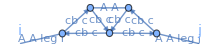
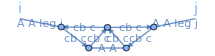
-Graphics-^-1= | -Graphics--1/2^ | -Graphics--1/2^ |  |

```mathematica
DSEPlot[X]
```

```mathematica
identifyGraphs[X,{{A,i},{A,j}}]
```

{{{1/2,op[V[{A,i},{cb,j3},{c,j1}],V[{A,j},{cb,l3},{c,l1}],V[{cb,j0},{cb,l0},{c,k0},{c,m0}],V[{A,m3},{cb,m1},{c,m2}],V[{A,k3},{cb,k1},{c,k2}],P[{c,j1},{cb,j0}],P[{c,l1},{cb,l0}],P[{c,m0},{cb,m1}],P[{c,k0},{cb,k1}],P[{A,m3},{A,k3}],P[{c,m2},{cb,l3}],P[{c,k2},{cb,j3}]]},{-1/2,op[V[{A,i},{cb,l3},{c,l1}],V[{A,j},{cb,j3},{c,j1}],V[{cb,l0},{cb,j0},{c,k0},{c,m0}],V[{A,m3},{cb,m1},{c,m2}],V[{A,k3},{cb,k1},{c,k2}],P[{c,j1},{cb,j0}],P[{c,l1},{cb,l0}],P[{c,m0},{cb,m1}],P[{c,k0},{cb,k1}],P[{A,m3},{A,k3}],P[{c,m2},{cb,l3}],P[{c,k2},{cb,j3}]]}}}

0

```mathematica
op[V[{A,i},{cb,j3},{c,j1}],V[{A,j},{cb,l3},{c,l1}],V[{cb,j0},{cb,l0},{c,k0},{c,m0}],V[{A,m3},{cb,m1},{c,m2}],V[{A,k3},{cb,k1},{c,k2}],P[{c,j1},{cb,j0}],P[{c,l1},{cb,l0}],P[{c,m0},{cb,m1}],P[{c,k0},{cb,k1}],P[{A,m3},{A,k3}],P[{c,m2},{cb,l3}],P[{c,k2},{cb,j3}]]//sortDummies//sE
-2X[[1]]//sortDummies//sE
```

Γ_(A cb c)^(i r1 r2) Γ_(A cb c)^(j s1 s2) Γ_(A cb c)^(v1 v2 w1) Γ_(A cb c)^(w2 x1 x2) Γ_(cb cb c c)^(t1 t2 u1 u2) Δ_(A A)^(v1 w2) Δ_(c cb)^(r2 t1) Δ_(c cb)^(s2 t2) Δ_(c cb)^(u1 x1) Δ_(c cb)^(u2 v2) Δ_(c cb)^(w1 s1) Δ_(c cb)^(x2 r1)

Γ_(A cb c)^(i t1 t2) Γ_(A cb c)^(j u1 u2) Γ_(A cb c)^(v1 v2 w1) Γ_(A cb c)^(w2 x1 x2) Γ_(cb cb c c)^(r1 r2 s1 s2) Δ_(A A)^(v1 w2) Δ_(c cb)^(s1 v2) Δ_(c cb)^(s2 x1) Δ_(c cb)^(t2 r1) Δ_(c cb)^(u2 r2) Δ_(c cb)^(w1 u1) Δ_(c cb)^(x2 t1)

```mathematica
op[V[{A,i},{cb,l3},{c,l1}],V[{A,j},{cb,j3},{c,j1}],V[{cb,l0},{cb,j0},{c,k0},{c,m0}],V[{A,m3},{cb,m1},{c,m2}],V[{A,k3},{cb,k1},{c,k2}],P[{c,j1},{cb,j0}],P[{c,l1},{cb,l0}],P[{c,m0},{cb,m1}],P[{c,k0},{cb,k1}],P[{A,m3},{A,k3}],P[{c,m2},{cb,l3}],P[{c,k2},{cb,j3}]]//sortDummies//sE
-2X[[2]]//sortDummies//sE
```

Γ_(A cb c)^(i r1 r2) Γ_(A cb c)^(j s1 s2) Γ_(A cb c)^(v1 v2 w1) Γ_(A cb c)^(w2 x1 x2) Γ_(cb cb c c)^(t1 t2 u1 u2) Δ_(A A)^(v1 w2) Δ_(c cb)^(r2 t1) Δ_(c cb)^(s2 t2) Δ_(c cb)^(u1 x1) Δ_(c cb)^(u2 v2) Δ_(c cb)^(w1 r1) Δ_(c cb)^(x2 s1)

Γ_(A cb c)^(i u1 u2) Γ_(A cb c)^(j t1 t2) Γ_(A cb c)^(v1 v2 w1) Γ_(A cb c)^(w2 x1 x2) Γ_(cb cb c c)^(r1 r2 s1 s2) Δ_(A A)^(v1 w2) Δ_(c cb)^(s1 v2) Δ_(c cb)^(s2 x1) Δ_(c cb)^(t2 r1) Δ_(c cb)^(u2 r2) Δ_(c cb)^(w1 u1) Δ_(c cb)^(x2 t1)

This should yield the sum of diagrams as they are identical.

sortCanonical is to blame:

Here, the two indices m0, k0 (totally internal) are exchanged.

```mathematica
X[[1]]
sortCanonical[%,{{A,i},{A,j}}]/.V[a___]:>Style[V[a],Red]
```

-1/2 op[V[{cb,j0},{cb,l0},{c,m0},{c,k0}],V[{A,i},{cb,j3},{c,j1}],V[{A,j},{cb,l3},{c,l1}],V[{A,m3},{cb,m1},{c,m2}],V[{A,k3},{cb,k1},{c,k2}],P[{c,j1},{cb,j0}],P[{c,l1},{cb,l0}],P[{c,m0},{cb,m1}],P[{c,k0},{cb,k1}],P[{A,m3},{A,k3}],P[{c,m2},{cb,l3}],P[{c,k2},{cb,j3}]]

{V[{cb,j0},{cb,l0},{c,m0},{c,k0}],V[{A,m3},{cb,m1},{c,m2}],V[{A,k3},{cb,k1},{c,k2}]}

<|i→1,j→2,j0→20000000001,k2→20000000001,l0→20000000002,m2→20000000002,j1→20000000001,j3→20000000001,l1→20000000002,l3→20000000002|>

1/2 op[V[{A,i},{cb,j3},{c,j1}],V[{A,j},{cb,l3},{c,l1}],V[{cb,j0},{cb,l0},{c,k0},{c,m0}],V[{A,m3},{cb,m1},{c,m2}],V[{A,k3},{cb,k1},{c,k2}],P[{c,j1},{cb,j0}],P[{c,l1},{cb,l0}],P[{c,m0},{cb,m1}],P[{c,k0},{cb,k1}],P[{A,m3},{A,k3}],P[{c,m2},{cb,l3}],P[{c,k2},{cb,j3}]]

```mathematica
V[{cb,1},{cb,2},{c,k0},{c,m0}]
```

Here, the two indices m0, k0 (totally internal) AND j0, l0 (attached to external, now ordered 1, 2) are exchanged.

```mathematica
X[[2]]
sortCanonical[%,{{A,i},{A,j}}]/.V[a___]:>Style[V[a],Red]
```

-1/2 op[V[{cb,j0},{cb,l0},{c,m0},{c,k0}],V[{A,j},{cb,j3},{c,j1}],V[{A,i},{cb,l3},{c,l1}],V[{A,m3},{cb,m1},{c,m2}],V[{A,k3},{cb,k1},{c,k2}],P[{c,j1},{cb,j0}],P[{c,l1},{cb,l0}],P[{c,m0},{cb,m1}],P[{c,k0},{cb,k1}],P[{A,m3},{A,k3}],P[{c,m2},{cb,l3}],P[{c,k2},{cb,j3}]]

<|i→1,j→2,j0→20000000002,k2→20000000002,l0→20000000001,m2→20000000001,j1→20000000002,j3→20000000002,l1→20000000001,l3→20000000001|>

-1/2 op[V[{A,i},{cb,l3},{c,l1}],V[{A,j},{cb,j3},{c,j1}],V[{cb,l0},{cb,j0},{c,k0},{c,m0}],V[{A,m3},{cb,m1},{c,m2}],V[{A,k3},{cb,k1},{c,k2}],P[{c,j1},{cb,j0}],P[{c,l1},{cb,l0}],P[{c,m0},{cb,m1}],P[{c,k0},{cb,k1}],P[{A,m3},{A,k3}],P[{c,m2},{cb,l3}],P[{c,k2},{cb,j3}]]

```mathematica
V[{cb,1},{cb,2},{c,k0},{c,m0}]
```

```mathematica
DSEPlot[eomPropPre[[-1]],fieldStyles,output->List]
```

-Graphics--1/2^

```mathematica
sortCanonical[eomPropPre[[-1]],{{phi,i},{phi,j}}]/.V[a___]:>Style[V[a],Red]
```

<|i→1,j→2,i1s→20000000001,i2s→20000000001,i5→20000000002,i6→20000000002,i1→20000000001,i2→20000000001,i5s→20000000002,i6s→20000000002|>

-1/2 op[V[{phi,i},{phi,i1},{phi,i2}],V[{phi,j},{phi,i5s},{phi,i6s}],V[{phi,i1s},{phi,i5},{phi,i4}],V[{phi,i2s},{phi,i6},{phi,i4s}],P[{phi,i1},{phi,i1s}],P[{phi,i2},{phi,i2s}],P[{phi,i4},{phi,i4s}],P[{phi,i5},{phi,i5s}],P[{phi,i6},{phi,i6s}]]

It seems that indices from internal propagators (not attached to an external vertex) do not get assigned a number.

## ToDos

Ensure that propagator derivatives are done correctly if definition order of fields is wrong for fermions.
What about mixed fields?

Not implemented for mixed propagators.

Permutations unclear: Necessary for bosons, but fermions do not work properly. --> Solved?

Document modFunc in identifyGraphs.

SyntaxInformation: See package, at the end.

Documentation: Usages for new functions.

Plot functions.

Update listOfAllFunctions in DoFun dir.

Still applicable?
Refactor DSEPlotGraph to be used in DSEGraphPlotList.
Permutations: extend to props.
Diag 5 in prop makes problems. Is in identifyGraphs, so maybe skip and wait if I can generalize identifyGraphsViaGraphs.
Prop derivs do not contain permutations.

Usages:
clipExt...
diffP
diffV
NPIPlot: if derivation of eom is improved, update here

# Development

## Minimal example: plotting, derivP, derivV

derivP, derivV are implemented as diffP, diffV.

```mathematica
setFields[{phi}];
```

```mathematica
fieldStyles={{phi,Black}};
```

```mathematica
action3PI=op[V[{phi,i1},{phi,i2},{phi,i3}],P[{phi,i1},{phi,i1s}],P[{phi,i3},{phi,i3s}],P[{phi,i2},{phi,i2s}],V[{phi,i1s},{phi,i2s},{phi,i3s}]]
```

op[V[{phi,i1},{phi,i2},{phi,i3}],P[{phi,i1},{phi,i1s}],P[{phi,i3},{phi,i3s}],P[{phi,i2},{phi,i2s}],V[{phi,i1s},{phi,i2s},{phi,i3s}]]

Plotting works:

```mathematica
DSEPlot[action3PI]
DSEPlot[action3PI,fieldStyles]
```

-Graphics-+^

-Graphics-+^

A first minimal working example of a derivative with respect to a propagator:

```mathematica
Clear@derivP
derivP[exp_op,P[{field1_,i1_},{field2_,i2_}]]:=Module[
{props,extP,res},
props=Cases[exp,P[{field1,_},{field2,_}]];
extP=P[{field1,i1},{field2,i2}];
res=Plus@@(Function[prop,exp/.prop:>Sequence[]/.{prop[[1,2]]:>i1,prop[[2,2]]:>i2}]/@props);
identifyGraphs[res,List@@extP]
]
```

```mathematica
derivP[action3PI,P[{phi,i},{phi,j}]]
DSEPlot[%,fieldStyles]
```

3 op[V[{phi,i},{phi,i1},{phi,i2}],V[{phi,j},{phi,i1s},{phi,i2s}],P[{phi,i1},{phi,i1s}],P[{phi,i2},{phi,i2s}]]

-Graphics-+3^

A first minimal working example of a derivative with respect to a vertex:

```mathematica
Clear@derivV
derivV[exp_op,V[fieldsInds___]]:=Module[
{vertices,extV,inds,indRules},
inds={fieldsInds}[[All,2]];
indRules[vert_]:=Thread[Rule[List@@vert[[All,2]],inds]];
vertices=Cases[exp,V[fieldsInds]/.{a_?fieldQ,b_}:>{a,_}];

Plus@@(Function[vert,exp/.vert:>Sequence[]/.indRules[vert]]/@vertices)
(*Thread[Rule[List@@vertices[[1]][[All,2]],inds]]*)
]
```

```mathematica
Clear@clipExtProps
clipExtProps[exp_op]:=Module[{extProps,indRules,extInds,extPropsDirected},

extInds=Cases[exp,{f1_?fieldQ,i_}:>i/;Count[exp,i,∞]==1,∞];
extProps=Cases[exp,P[{f1_,i1_},{f2_,i2_}]/;MemberQ[extInds,i1|i2]];

(* adjust indices for replacement rules *)
extPropsDirected=extProps/.{P[{f1_,i1_},{f2_,i2_}]:>P[{f2,i2},{f1,i1}]/;MemberQ[extInds,i1]};

indRules=Rule@@@extPropsDirected;

(* delete propagator and adjust indices *)
exp/.(#:>Sequence[]&/@extProps)/.indRules
]
```

```mathematica
derivV[action3PI,V[{phi,i},{phi,j},{phi,k}]]
%[[1]]
clipExtProps[%]
DSEPlot[%,fieldStyles]
```

op[P[{phi,i},{phi,i1s}],P[{phi,k},{phi,i3s}],P[{phi,j},{phi,i2s}],V[{phi,i1s},{phi,i2s},{phi,i3s}]]+op[V[{phi,i1},{phi,i2},{phi,i3}],P[{phi,i1},{phi,i}],P[{phi,i3},{phi,k}],P[{phi,i2},{phi,j}]]

op[P[{phi,i},{phi,i1s}],P[{phi,k},{phi,i3s}],P[{phi,j},{phi,i2s}],V[{phi,i1s},{phi,i2s},{phi,i3s}]]

op[V[{phi,i},{phi,j},{phi,k}]]

-Graphics-+^

## IsomorphicGraphQ enhancement

--> Not feasible because external points are not distinguished. For example, the three swordfish diagrams would be the same. Also problems with multi edges (not clear how to resolve, colored edges suggested by Jonas) and mixing of bosons and fermions (would require an extra function for separation).

IsomorphicGraphQ does not work for
1. multiple edges of the same type connecting the same vertex
2. mixing undirected and directed edges

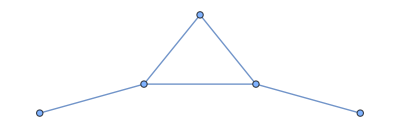

```mathematica
graph1=Graph[{UndirectedEdge[1,2],UndirectedEdge[2,3],UndirectedEdge[3,4],UndirectedEdge[4,2],UndirectedEdge[4,5]}]
```

```mathematica
graph2=Graph[{UndirectedEdge[1,2],UndirectedEdge[2,10],UndirectedEdge[10,4],UndirectedEdge[4,2],UndirectedEdge[4,5]}]
```

-Graphics-

```mathematica
graph1==graph2
```

False

```mathematica
IsomorphicGraphQ[graph1,graph2]
```

True

```mathematica
graph3=Graph[{UndirectedEdge[1,2],UndirectedEdge[2,3],UndirectedEdge[3,2],UndirectedEdge[3,5]}]
```

-Graphics-

```mathematica
graph4=Graph[{UndirectedEdge[1,2],UndirectedEdge[2,30],UndirectedEdge[30,2],UndirectedEdge[30,5]}]
```

-Graphics-

```mathematica
IsomorphicGraphQ[graph3,graph4]
```

IsomorphicGraphQ::ngen: The generalized … is not implemented.

IsomorphicGraphQ[-Graphics-,-Graphics-]

Modify multiple labels:

```mathematica
graph3a=Graph[{UndirectedEdge[1,2],UndirectedEdge[2,3],UndirectedEdge[3,2],UndirectedEdge[3,5]}]
```

```mathematica
Graph[{UndirectedEdge[1,2],UndirectedEdge[2,3],UndirectedEdge[3,2],UndirectedEdge[3,5]}]
```

```mathematica
Names["*Edge*Col*"]
```

{EdgeColor,FindEdgeColoring}

```mathematica
??EdgeColor
```

```mathematica
??FindEdgeColoring
```

```mathematica
FindEdgeColoring[graph1]
```

{2,3,2,1,3}

{3,2,1,3}

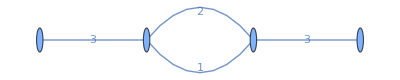

```mathematica
cols3a=FindEdgeColoring[graph3]
graph3a=GraphPlot[{{UndirectedEdge[1,2],"3"},{UndirectedEdge[2,3],"2"},{UndirectedEdge[3,2],"1"},{UndirectedEdge[3,5],"3"}}]
```

```mathematica
cols4a=FindEdgeColoring[graph4]
graph4a=GraphPlot[{{UndirectedEdge[1,2],"3"},{UndirectedEdge[2,30],"2"},{UndirectedEdge[30,2],"1"},{UndirectedEdge[30,5],"3"}}]
```

{3,2,1,3}

-Graphics-

```mathematica
IsomorphicGraphQ[graph3a,graph4a]
```

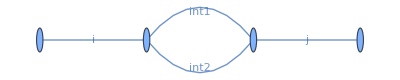

```mathematica
graph3b=GraphPlot[{{UndirectedEdge[1,2],"i"},{UndirectedEdge[2,3],"int1"},{UndirectedEdge[3,2],"int2"},{UndirectedEdge[3,5],"j"}}]
```

```mathematica
graph4b=GraphPlot[{{UndirectedEdge[1,2],"i"},{UndirectedEdge[2,3],"int1"},{UndirectedEdge[3,2],"int2"},{UndirectedEdge[3,5],"j"}}]
```

-Graphics-

```mathematica
IsomorphicGraphQ[graph3b,graph4b]
```

False

```mathematica
graph3b-graph4b
```

0

## Fermionic example (YM, 3PI)

### Definitions

```mathematica
setFields[{A},{{c,cb}}];
```

```mathematica
fieldStyles={{A,Red},{psi,Blue},{c,Green}};
```

```mathematica
actionYM3PI=(* eight *)1/8op[S[{A,i1},{A,i2},{A,i3},{A,i4}],P[{A,i1},{A,i2}],P[{A,i3},{A,i4}]]+(* sunset SV gluon *)1/6op[S[{A,i1},{A,i2},{A,i3}],P[{A,i1},{A,i1s}],P[{A,i3},{A,i3s}],P[{A,i2},{A,i2s}],V[{A,i1s},{A,i2s},{A,i3s}]]-(* sunset SV ghost-gluon*)op[S[{A,i1},{cb,i2},{c,i3}],P[{A,i1},{A,i1s}],P[{c,i3},{cb,i3s}],P[{c,i2s},{cb,i2}],V[{A,i1s},{cb,i3s},{c,i2s}]]+(* eye *)1/48op[S[{A,i1},{A,i2},{A,i3},{A,i4}],P[{A,i1},{A,i1s}],P[{A,i3},{A,i3s}],P[{A,i2},{A,i2s}],P[{A,i4},{A,i4s}],S[{A,i1s},{A,i2s},{A,i3s},{A,i4s}]]+(* double squint *)1/8op[S[{A,i1},{A,i2},{A,i3},{A,i4}],P[{A,i1},{A,i1s}],P[{A,i3},{A,i3s}],P[{A,i2},{A,i2s}],P[{A,i4},{A,i4s}],P[{A,i5},{A,i5s}],V[{A,i1s},{A,i2s},{A,i5}],V[{A,i3s},{A,i4s},{A,i5s}]]-(* sunset VV gluon *)1/12op[V[{A,i1},{A,i2},{A,i3}],P[{A,i1},{A,i1s}],P[{A,i3},{A,i3s}],P[{A,i2},{A,i2s}],V[{A,i1s},{A,i2s},{A,i3s}]]+(* sunset VV ghost-gluon*)1/2op[V[{A,i1},{cb,i2},{c,i3}],P[{A,i1},{A,i1s}],P[{c,i3},{cb,i3s}],P[{c,i2s},{cb,i2}],V[{A,i1s},{cb,i3s},{c,i2s}]]+(* star gluon *)1/24op[V[{A,i1},{A,i2},{A,i3}],P[{A,i1},{A,i1s}],P[{A,i3},{A,i3s}],P[{A,i2},{A,i2s}],V[{A,i1s},{A,i4},{A,i5}],P[{A,i4},{A,i4s}],P[{A,i5},{A,i5s}],V[{A,i2s},{A,i4s},{A,i6}],P[{A,i6},{A,i6s}],V[{A,i3s},{A,i5s},{A,i6s}]]-(* star ghost-gluon Abelian *)1/4op[V[{A,i1},{cb,i5},{c,i8s}],
V[{A,i2},{cb,i6},{c,i5s}],
V[{A,i3},{cb,i7},{c,i6s}],
V[{A,i4},{cb,i8},{c,i7s}],
P[{A,i1},{A,i3}],P[{A,i2},{A,i4}],
P[{c,i5s},{cb,i5}],P[{c,i6s},{cb,i6}],P[{c,i7s},{cb,i7}],P[{c,i8s},{cb,i8}]]-(* star ghost-gluon non-Abelian *)1/3op[V[{A,i1},{A,i2},{A,i3}],
V[{A,i1s},{cb,i4},{c,i5s}],
V[{A,i2s},{cb,i5},{c,i6s}],
V[{A,i3s},{cb,i6},{c,i4s}],
P[{A,i1},{A,i1s}],P[{A,i2},{A,i2s}],P[{A,i3},{A,i3s}],
P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]];
```

```mathematica
DSEPlot[actionYM3PI,fieldStyles]
```

Γ^k^= | -Graphics-+1/8^-1 | -Graphics-+1/6^ | -Graphics--^ | -Graphics--1/12^
 | -Graphics-+1/2^ | -Graphics-+1/48^ | -Graphics-+1/8^ | -Graphics-+1/24^
 | -Graphics--1/3^ | -Graphics--1/4^ |  |

### Vertices

#### AAA

```mathematica
eomAAADiagsPre=derivV[actionYM3PI,V[{A,i},{A,j},{A,k}]];
eomAAADiagsPreId=identifyGraphs[clipExtProps@eomAAADiagsPre,{{A,i},{A,j},{A,k}}];
```

```mathematica
DSEPlot[eomAAADiagsPreId,fieldStyles,output->List]
```

{-Graphics-+1/6^,-Graphics--1/6^,-Graphics-+1/12^,-Graphics-+1/12^,-Graphics-+1/12^,-Graphics-+1/6^,-Graphics--1/3^}

Select diagrams:

```mathematica
eomAAA=6eomAAADiagsPreId[[{1,3,4,5,6,7}]]//Expand;
```

```mathematica
DSEPlot[eomAAA,fieldStyles]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+^ | -Graphics--2^ |  |

#### Acbc

```mathematica
eomAcbcDiagsPre=derivV[actionYM3PI,V[{A,i},{cb,k},{c,j}]];
eomAcbcDiagsPreId=identifyGraphs[clipExtProps@eomAcbcDiagsPre,{{A,i},{cb,j},{c,k}}];
```

Note: The derivative with respect to V[{A, i}, {cb, j}, {c, k}] yields as external legs {{A, i}, {c, j}, {c, k}}!

```mathematica
eomAcbcDiagsPre=derivV[actionYM3PI,V[{A,i},{cb,k},{c,j}]];
eomAcbcDiagsPreId=identifyGraphs[clipExtProps@eomAcbcDiagsPre,{{A,i},{antiField@cb,k},{antiField@c,j}}];
```

```mathematica
eomAcbcDiagsPreId[[3]]
```

-op[V[{A,i},{A,i1},{A,i3}],V[{A,i1s},{cb,i4},{c,k}],V[{A,i3s},{cb,j},{c,i4s}],P[{A,i1},{A,i1s}],P[{A,i3},{A,i3s}],P[{c,i4s},{cb,i4}]]

```mathematica
DSEPlot[eomAcbcDiagsPreId,fieldStyles,output->List]
```

{-Graphics--^,-Graphics-+^,-Graphics--^,-Graphics--^}

Select diagrams:

```mathematica
eomAcbc=-eomAcbcDiagsPreId[[{1,3,4}]]//Expand;
```

```mathematica
DSEPlot[eomAcbc,fieldStyles]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ |

### Propagators

#### AA

```mathematica
eomAAPre=op[S[{A,i},{A,j}]]-2derivPop[actionYM3PI,P[{A,i},{A,j}]]//Expand;
```

```mathematica
eomAAPre=identifyGraphs[op[S[{A,i},{A,j}]]-2derivPDo[actionYM3PI,P[{A,i},{A,j}]]//Expand,{{A,i},{A,j}}];
```

```mathematica
DSEPlot[eomAAPre,fieldStyles,output->List]
```

{-Graphics-+^-1,-Graphics--1/2^,-Graphics--1/2^,-Graphics-+^,-Graphics-+1/2^,-Graphics--1/2^,-Graphics--^,-Graphics-+^,-Graphics--1/6^,-Graphics--1/2^,-Graphics--1/4^,-Graphics--1/2^,-Graphics--1/2^,-Graphics-+^,-Graphics-+^,-Graphics-+^}

{-Graphics-+^-1,-Graphics--1/2^,-Graphics--^,-Graphics-+2^,-Graphics-+1/2^,-Graphics--^,-Graphics--1/6^,-Graphics--^,-Graphics--1/4^,-Graphics--1/2^,-Graphics-+2^,-Graphics-+^}

Put in vertex eoms (derivations elsewhere):

```mathematica
DSEPlot[eomAAA,fieldStyles]
DSEPlot[eomAcbc,fieldStyles]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+^ | -Graphics--2^ |  |

-Graphics-^= | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ |

Manual replacement of vertex.

```mathematica
Clear[dummyRules]
dummyRules[a_ exp_op,rest___]:=dummyRules[exp,rest]
dummyRules[exp_op,extFields_List]:=Module[{intInds,dummies},
intInds=Union@DeleteCases[Cases[exp,{A|cb|c,i_}:>i,∞],Alternatives@@extFields[[All,2]]];

Thread@Rule[intInds,Table[insDummy[],{Length@intInds}]]
]
```

```mathematica
Clear@vertReplsAAA
vertReplsAAA[i_,j_,k_]=Expand[eomAAA/.a_op:>(a/.dummyRules[a,{{A,i},{A,j},{A,k}}])];
```

```mathematica
Clear@vertReplsAcbc
vertReplsAcbc[i_,j_,k_]=Expand[eomAcbc/.a_op:>(a/.dummyRules[a,{{A,i},{cb,j},{c,k}}])];
```

```mathematica
DSEPlot[eomAAPre,fieldStyles,output->List]
```

{-Graphics-+^-1,-Graphics--1/2^,-Graphics--1/2^,-Graphics-+^,-Graphics-+1/2^,-Graphics--1/2^,-Graphics--^,-Graphics-+^,-Graphics--1/6^,-Graphics--1/2^,-Graphics--1/4^,-Graphics--1/2^,-Graphics--1/2^,-Graphics-+^,-Graphics-+^,-Graphics-+^}

Show results of replacement of the dressed vertex in the third diagram:

```mathematica
DSEPlot[eomAAPre[[5]],fieldStyles]
DSEPlot[eomAAPre[[5]]/.V[{A,i},{A,i1_},{A,i2_}]:>vertReplsAAA[i,i1,i2]//Expand,fieldStyles,output->List]
```

-Graphics-+1/2^

{-Graphics-+1/2^,-Graphics-+1/4^,-Graphics-+1/4^,-Graphics-+1/4^,-Graphics-+1/2^,-Graphics--^}

```mathematica
DSEPlot[eomAAPre[[7]],fieldStyles]
DSEPlot[eomAAPre[[7]]/.V[{A,i},{cb,i1_},{c,i2_}]:>vertReplsAcbc[i,i1,i2]//Expand,fieldStyles,output->List]
```

-Graphics--^

{-Graphics--^,-Graphics--^,-Graphics--^}

Perform manual replacement of the vertex in one diagram:

```mathematica
eomAAPre2=eomAAPre[[{1,2,3,4,6,8,9,10,11,12,13,14,15,16}]]+(eomAAPre[[5]]/.V[{A,i},{A,i1_},{A,i2_}]:>vertReplsAAA[i,i1,i2])+(eomAAPre[[7]]/.V[{A,i},{cb,i1_},{c,i2_}]:>vertReplsAcbc[i,i1,i2]);
DSEPlot[eomAAPre2,fieldStyles]
eomAA=identifyGraphs[eomAAPre2,{{A,i},{A,j}}];
DSEPlot[eomAA,fieldStyles]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--1/6^ | -Graphics--1/2^ | -Graphics-+1/4^ | -Graphics-+1/4^
 | -Graphics--1/4^ | -Graphics--1/2^ | -Graphics-+1/4^ | -Graphics--1/2^
 | -Graphics-+^ | -Graphics-+1/2^ | -Graphics--^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics--^ |

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--1/6^ | -Graphics--1/2^ |  |

```mathematica
eomAAPre2=eomAAPre[[{1,2,3,4,6,8,9,10,11,12,13,14,15,16}]]+(eomAAPre[[5]]/.V[{A,j},{A,i1_},{A,i2_}]:>vertReplsAAA[j,i1,i2])+(eomAAPre[[7]]/.V[{A,j},{cb,i1_},{c,i2_}]:>vertReplsAcbc[j,i1,i2]);
DSEPlot[eomAAPre2,fieldStyles]
eomAA=identifyGraphs[eomAAPre2,{{A,i},{A,j}}];
DSEPlot[eomAA,fieldStyles]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics-+1/2^ | -Graphics--1/2^ | -Graphics--^ | -Graphics-+^
 | -Graphics--1/6^ | -Graphics--1/2^ | -Graphics-+1/4^ | -Graphics-+1/4^
 | -Graphics-+1/4^ | -Graphics--1/4^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics-+1/2^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ |

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--1/6^ | -Graphics--1/2^ |  |

#### cbc

Note the different prefactor in front of the derivative due to fermions (+1 instead of -2).

```mathematica
eomcbcPre=op[S[{cb,i},{c,j}]]+derivPop[actionYM3PI,P[{c,i},{cb,j}]]//Expand;
```

```mathematica
DSEPlot[eomcbcPre,fieldStyles,output->List]
```

{-Graphics-+^-1,-Graphics--1/2^,-Graphics-+1/2^,-Graphics--1/2^,-Graphics--1/2^,-Graphics--1/2^}

Put in vertex eom (derivation elsewhere):

```mathematica
DSEPlot[eomAcbc,fieldStyles]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ |

Manual replacement of vertex.

```mathematica
Clear[dummyRules]
dummyRules[a_ exp_op,rest___]:=dummyRules[exp,rest]
dummyRules[exp_op,extFields_List]:=Module[{intInds,dummies},
intInds=Union@DeleteCases[Cases[exp,{A|cb|c,i_}:>i,∞],Alternatives@@extFields[[All,2]]];

Thread@Rule[intInds,Table[insDummy[],{Length@intInds}]]
]
```

```mathematica
Clear@vertReplsAcbc
vertReplsAcbc[i_,j_,k_]=Expand[eomAcbc/.a_op:>(a/.dummyRules[a,{{A,i},{cb,j},{c,k}}])];
```

```mathematica
DSEPlot[eomcbcPre,fieldStyles,output->List]
```

{-Graphics-+^-1,-Graphics--^,-Graphics-+^,-Graphics--^,-Graphics--^,-Graphics--^}

Show results of replacement of the dressed vertex in the third diagram:

```mathematica
DSEPlot[eomcbcPre[[3]],fieldStyles]
DSEPlot[eomcbcPre[[3]]/.V[{A,i1_},{cb,i2_},{c,i}]:>vertReplsAcbc[i1,i2,i]//Expand,fieldStyles,output->List]
```

-Graphics-+^

{-Graphics-+^,-Graphics-+^,-Graphics-+^}

Perform manual replacement of the vertex in one diagram:

```mathematica
eomcbcPre2=eomcbcPre[[{1,2,4,5,6}]]+(eomcbcPre[[3]]/.V[{A,i1_},{cb,i2_},{c,i}]:>vertReplsAcbc[i1,i2,i]);
DSEPlot[eomcbcPre2,fieldStyles]
eomcbc=identifyGraphs[eomcbcPre2,{{c,i},{cb,j}}];
DSEPlot[eomcbc,fieldStyles]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--^ | -Graphics-+^ | -Graphics--^
 | -Graphics-+^ | -Graphics--^ |  |

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--^ |  |

### Kernels

```mathematica
DSEPlot[actionYM3PI,fieldStyles]
```

Γ^k^= | -Graphics-+1/8^-1 | -Graphics-+1/6^ | -Graphics--^ | -Graphics--1/12^
 | -Graphics-+1/2^ | -Graphics-+1/48^ | -Graphics-+1/8^ | -Graphics-+1/24^
 | -Graphics--1/3^ | -Graphics--1/4^ |  |

#### GlGl (Cancellations not realized at the end)

```mathematica
kerGlGlDer1=identifyGraphs[2diffP[actionYM3PI,P[{A,i},{A,j}]]//Expand,{{A,i},{A,j}}];
DSEPlot[kerGlGlDer1,fieldStyles]
kerGlGlDer2=identifyGraphs[diffP[kerGlGlDer1,P[{A,k},{A,l}]],{{A,i},{A,j},{A,k},{A,l}}];
DSEPlot[kerGlGlDer2,fieldStyles]
```

-Graphics-^-1= | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--^ | -Graphics--1/2^
 | -Graphics-+1/2^ | -Graphics-+^ | -Graphics--^ | -Graphics-+1/6^
 | -Graphics-+1/2^ | -Graphics-+1/4^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ |

-Graphics-^= | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--1/2^
 | -Graphics-+1/2^ | -Graphics--1/2^ | -Graphics-+1/2^ | -Graphics-+1/4^
 | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics-+1/2^
 | -Graphics-+1/4^ | -Graphics-+1/2^ | -Graphics-+1/4^ | -Graphics-+1/4^
 | -Graphics-+1/4^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/4^
 | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics-+1/4^
 | -Graphics-+1/4^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics--^ | -Graphics-+1/2^ | -Graphics--^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ |  |

Manual replacement of vertex. Here it is the bare ones.

```mathematica
Clear[dummyRules]
dummyRules[a_ exp_op,rest___]:=dummyRules[exp,rest]
dummyRules[exp_op,extFields_List]:=Module[{intInds,dummies},
intInds=Union@DeleteCases[Cases[exp,{A|cb|c,i_}:>i,∞],Alternatives@@extFields[[All,2]]];

Thread@Rule[intInds,Table[insDummy[],{Length@intInds}]]
]
```

```mathematica
Clear@vertReplsAAA
vertReplsAAA[i_,j_,k_]=Expand[op[V[{A,i},{A,j},{A,k}]]-eomAAA[[2;;-1]]/.a_op:>(a/.dummyRules[a,{{A,i},{A,j},{A,k}}])];
```

Perform manual replacement of the vertex in one diagram:

```mathematica
diagsRepl1={2,3};
diagsRepl2={5,7};
diagsNotAlt=Delete[Range[Length[kerGlGlDer2]],{#}&/@Join[diagsRepl1,diagsRepl2]]
```

{1,4,6,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38}

```mathematica
DSEPlot[kerGlGlDer2[[diagsRepl1]],fieldStyles]
DSEPlot[kerGlGlDer2[[diagsRepl1]]/.S[{A,i},{A,i1_},{A,i2_}]:>vertReplsAAA[i,i1,i2]//Expand,fieldStyles,output->List]
```

-Graphics-^= | -Graphics-+1/2^ | -Graphics-+1/2^ |  |

{-Graphics-+1/2^,-Graphics-+1/2^,-Graphics--1/4^,-Graphics--1/4^,-Graphics--1/4^,-Graphics--1/4^,-Graphics--1/4^,-Graphics--1/4^,-Graphics--1/2^,-Graphics--1/2^,-Graphics-+^,-Graphics-+^}

```mathematica
DSEPlot[kerGlGlDer2[[diagsRepl2]],fieldStyles]
DSEPlot[kerGlGlDer2[[diagsRepl2]]/.S[{A,j},{A,i1_},{A,i2_}]:>vertReplsAAA[j,i1,i2]//Expand,fieldStyles,output->List]
```

-Graphics-^= | -Graphics-+1/2^ | -Graphics-+1/2^ |  |

{-Graphics-+1/2^,-Graphics-+1/2^,-Graphics--1/4^,-Graphics--1/4^,-Graphics--1/4^,-Graphics--1/4^,-Graphics--1/4^,-Graphics--1/4^,-Graphics--1/2^,-Graphics-+^,-Graphics--1/2^,-Graphics-+^}

Using modFunc argument to use symmetry in legs.

```mathematica
kerGlGlDer2ResummedPre=kerGlGlDer2[[diagsNotAlt]]+(kerGlGlDer2[[diagsRepl1]]/.S[{A,i},{A,i1_},{A,i2_}]:>vertReplsAAA[i,i1,i2])+(kerGlGlDer2[[diagsRepl2]]/.S[{A,j},{A,i1_},{A,i2_}]:>vertReplsAAA[j,i1,i2]);
DSEPlot[kerGlGlDer2ResummedPre,fieldStyles]
kerGlGlDer2Resummed=identifyGraphs[kerGlGlDer2ResummedPre,{{A,i},{A,j},{A,k},{A,l}},(#/.l:>k&)];
DSEPlot[kerGlGlDer2Resummed,fieldStyles]
```

-Graphics-^= | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/4^
 | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics--1/4^
 | -Graphics--1/4^ | -Graphics-+1/2^ | -Graphics-+1/4^ | -Graphics--1/4^
 | -Graphics-+1/2^ | -Graphics-+1/4^ | -Graphics--1/4^ | -Graphics-+1/4^
 | -Graphics-+1/4^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--1/4^
 | -Graphics--1/4^ | -Graphics-+1/4^ | -Graphics--1/4^ | -Graphics-+1/4^
 | -Graphics-+1/4^ | -Graphics--1/4^ | -Graphics--1/4^ | -Graphics-+1/4^
 | -Graphics--1/4^ | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics--1/4^
 | -Graphics--1/4^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics--^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics-+1/2^ | -Graphics--^ | -Graphics--1/2^ | -Graphics-+^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics-+^ | -Graphics-+^ |  |

-Graphics-^= | -Graphics-+1/2^ | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+1/2^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ |  |  |

Realize symmetry in k,l:
Identify k and l in identification process.
Missing: fermion triangle.

Triangles differ only in direction:

```mathematica
kerGlGlDer2Resummed[[7;;8]]
```

-op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,k},{A,i2}],V[{A,l},{cb,i6},{c,i4s}],V[{A,i2s},{cb,i5},{c,i6s}],P[{A,i2},{A,i2s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]+op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,k},{A,i3}],V[{A,l},{cb,i5},{c,i6s}],V[{A,i3s},{cb,i6},{c,i4s}],P[{A,i3},{A,i3s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]

```mathematica
identifyGraphs[kerGlGlDer2Resummed[[7;;8]],{{A,i},{A,j},{A,k},{A,l}}]
DSEPlot[%,fieldStyles]
```

-op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,k},{A,i2}],V[{A,l},{cb,i6},{c,i4s}],V[{A,i2s},{cb,i5},{c,i6s}],P[{A,i2},{A,i2s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]+op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,k},{A,i3}],V[{A,l},{cb,i5},{c,i6s}],V[{A,i3s},{cb,i6},{c,i4s}],P[{A,i3},{A,i3s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]

-Graphics-^= | -Graphics--^ | -Graphics-+^ |  |

```mathematica
-op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,k},{A,i2}],V[{A,l},{cb,i6},{c,i4s}],V[{A,i2s},{cb,i5},{c,i6s}],P[{A,i2},{A,i2s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]+op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,k},{A,i3}],V[{A,l},{cb,i5},{c,i6s}],V[{A,i3s},{cb,i6},{c,i4s}],P[{A,i3},{A,i3s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]
DSEPlot[%,fieldStyles]
identifyGraphs[%%,{{A,i},{A,j},{A,k},{A,l}}]
DSEPlot[%,fieldStyles]
```

-op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,k},{A,i2}],V[{A,l},{cb,i6},{c,i4s}],V[{A,i2s},{cb,i5},{c,i6s}],P[{A,i2},{A,i2s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]+op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,k},{A,i3}],V[{A,l},{cb,i5},{c,i6s}],V[{A,i3s},{cb,i6},{c,i4s}],P[{A,i3},{A,i3s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]

-Graphics-^= | -Graphics--^ | -Graphics-+^ |  |

-op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,k},{A,i2}],V[{A,l},{cb,i6},{c,i4s}],V[{A,i2s},{cb,i5},{c,i6s}],P[{A,i2},{A,i2s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]+op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,k},{A,i3}],V[{A,l},{cb,i5},{c,i6s}],V[{A,i3s},{cb,i6},{c,i4s}],P[{A,i3},{A,i3s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]

-Graphics-^= | -Graphics--^ | -Graphics-+^ |  |

Id works for triangles only:

```mathematica
-op[V[{A,i},{cb,i4},{c,i5s}],V[{A,l},{cb,i6},{c,i4s}],V[{A,i2s},{cb,i5},{c,i6s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]+op[V[{A,i},{cb,i4},{c,i5s}],V[{A,l},{cb,i5},{c,i6s}],V[{A,i2s},{cb,i6},{c,i4s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]
DSEPlot[%,fieldStyles]
identifyGraphs[%%,{{A,i},{A,l},{A,i2s}}]
DSEPlot[%,fieldStyles]
```

op[V[{A,i},{cb,i4},{c,i5s}],V[{A,l},{cb,i5},{c,i6s}],V[{A,i2s},{cb,i6},{c,i4s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]-op[V[{A,i},{cb,i4},{c,i5s}],V[{A,l},{cb,i6},{c,i4s}],V[{A,i2s},{cb,i5},{c,i6s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]

-Graphics-^= | -Graphics-+^ | -Graphics--^ |  |

0

0

```mathematica
-op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,k},{A,i20}],V[{A,l},{cb,i6},{c,i4s}],V[{A,i20s},{cb,i5},{c,i6s}],P[{A,i20},{A,i20s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]+op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,k},{A,i20}],V[{A,l},{cb,i5},{c,i6s}],V[{A,i20s},{cb,i6},{c,i4s}],P[{A,i20},{A,i20s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]//sortDummies
DSEPlot[%,fieldStyles]
identifyGraphs[%%,{{A,i},{A,j},{A,k},{A,l}}]
DSEPlot[%,fieldStyles]
```

op[V[{A,i},{cb,r1},{c,s1}],V[{A,j},{A,k},{A,t1}],V[{A,l},{cb,u1},{c,v1}],V[{A,w1},{cb,x1},{c,y1}],P[{A,t1},{A,w1}],P[{c,v1},{cb,x1}],P[{c,s1},{cb,u1}],P[{c,y1},{cb,r1}]]-op[V[{A,i},{cb,r1},{c,s1}],V[{A,j},{A,k},{A,t1}],V[{A,l},{cb,u1},{c,v1}],V[{A,w1},{cb,x1},{c,y1}],P[{A,t1},{A,w1}],P[{c,y1},{cb,u1}],P[{c,s1},{cb,x1}],P[{c,v1},{cb,r1}]]

-Graphics-^= | -Graphics-+^ | -Graphics--^ |  |

op[V[{A,i},{cb,r1},{c,s1}],V[{A,j},{A,k},{A,t1}],V[{A,l},{cb,u1},{c,v1}],V[{A,w1},{cb,x1},{c,y1}],P[{A,t1},{A,w1}],P[{c,v1},{cb,x1}],P[{c,s1},{cb,u1}],P[{c,y1},{cb,r1}]]-op[V[{A,i},{cb,r1},{c,s1}],V[{A,j},{A,k},{A,t1}],V[{A,l},{cb,u1},{c,v1}],V[{A,w1},{cb,x1},{c,y1}],P[{A,t1},{A,w1}],P[{c,y1},{cb,u1}],P[{c,s1},{cb,x1}],P[{c,v1},{cb,r1}]]

-Graphics-^= | -Graphics-+^ | -Graphics--^ |  |

```mathematica
identifyGraphs[kerGlGlDer2Resummed[[2;;3]],{{A,i},{A,j},{A,k},{A,l}},#/.k:>l&]
DSEPlot[%,fieldStyles]
```

op[V[{A,i},{A,k},{A,i1s}],V[{A,j},{A,l},{A,i1}],P[{A,i1},{A,i1s}]]+1/2 op[S[{A,i},{A,k},{A,i1},{A,i2}],P[{A,i1},{A,i1s}],P[{A,i2},{A,i2s}],S[{A,j},{A,l},{A,i1s},{A,i2s}]]

-Graphics-^= | -Graphics-+^ | -Graphics-+1/2^ |  |

```mathematica
identifyGraphs[1/2 op[V[{A,i},{A,k},{A,i1s}],V[{A,j},{A,l},{A,i1}],P[{A,i1},{A,i1s}]]+1/2 op[V[{A,i},{A,k},{A,i1s}],V[{A,j},{A,l},{A,i1}],P[{A,i1},{A,i1s}]],{{A,i},{A,j},{A,k},{A,l}}];
DSEPlot[%,fieldStyles]
```

-Graphics-+^

```mathematica
identifyGraphs[kerGlGlDer2Resummed[[2;;3]]/.l:>k,{{A,i},{A,j},{A,k},{A,l}}];
DSEPlot[%,fieldStyles]
```

-Graphics-+^

```mathematica
identifyGraphs[kerGlGlDer2Resummed/.l:>k,{{A,i},{A,j},{A,k},{A,l}}];
DSEPlot[%,fieldStyles]
```

-Graphics-^-1= | -Graphics-+1/2^-1 | -Graphics-+^ | -Graphics-+1/2^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+1/2^ | -Graphics--^ | -Graphics-+^
 | -Graphics--^ |  |  |

```mathematica
{{-Graphics-Overscript["", "-1"]"=", "+"1/2Overscript["", "-1"], "+"Overscript["", ""], "+"1/2Overscript["", ""], "+"Overscript["", ""]}, {"", "+"Overscript["", ""], "+"1/2Overscript["", ""], -Graphics-"-"Overscript["", ""], -Graphics-"+"Overscript["", ""]}, {"", "-"Overscript["", ""], "", "", ""}}
```

```mathematica
kerGlGlDer2Resummed[[13;;14]]
```

-1/2 op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,l},{A,i2}],V[{A,k},{cb,i6},{c,i4s}],V[{A,i2s},{cb,i5},{c,i6s}],P[{A,i2},{A,i2s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]+1/2 op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,l},{A,i3}],V[{A,k},{cb,i5},{c,i6s}],V[{A,i3s},{cb,i6},{c,i4s}],P[{A,i3},{A,i3s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]

```mathematica
identifyGraphs[-1/2 op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,l},{A,i2}],V[{A,k},{cb,i6},{c,i4s}],V[{A,i2s},{cb,i5},{c,i6s}],P[{A,i2},{A,i2s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]+1/2 op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,l},{A,i3}],V[{A,k},{cb,i5},{c,i6s}],V[{A,i3s},{cb,i6},{c,i4s}],P[{A,i3},{A,i3s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]],{{A,i},{A,j},{A,k},{A,l}}]
```

-1/2 op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,l},{A,i2}],V[{A,k},{cb,i6},{c,i4s}],V[{A,i2s},{cb,i5},{c,i6s}],P[{A,i2},{A,i2s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]+1/2 op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,l},{A,i3}],V[{A,k},{cb,i5},{c,i6s}],V[{A,i3s},{cb,i6},{c,i4s}],P[{A,i3},{A,i3s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]

```mathematica
identifyGraphs[-1/2 op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,l},{A,i2}],V[{A,k},{cb,i6},{c,i4s}],V[{A,i2s},{cb,i5},{c,i6s}],P[{A,i2},{A,i2s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]+1/2 op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,l},{A,i3}],V[{A,k},{cb,i5},{c,i6s}],V[{A,i3s},{cb,i6},{c,i4s}],P[{A,i3},{A,i3s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]],{{A,i},{A,j},{A,k},{A,l}},#/.k:>l&]
DSEPlot[%,fieldStyles]
```

{{{-1/2,op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,l},{A,i2}],V[{A,k},{cb,i6},{c,i4s}],V[{A,i2s},{cb,i5},{c,i6s}],P[{A,i2},{A,i2s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]},{1/2,op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,l},{A,i3}],V[{A,k},{cb,i5},{c,i6s}],V[{A,i3s},{cb,i6},{c,i4s}],P[{A,i3},{A,i3s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]}}}

-1/2 op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,l},{A,i2}],V[{A,k},{cb,i6},{c,i4s}],V[{A,i2s},{cb,i5},{c,i6s}],P[{A,i2},{A,i2s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]+1/2 op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,l},{A,i3}],V[{A,k},{cb,i5},{c,i6s}],V[{A,i3s},{cb,i6},{c,i4s}],P[{A,i3},{A,i3s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]

-Graphics-^= | -Graphics--1/2^ | -Graphics-+1/2^ |  |

```mathematica
{
  Sort@Cases[#1, P[q1_, q2_] :> {q1[[1]], q2[[1]]}, 2],
  Sort[(Cases[#, V[__]|CO[__], 2]/. {Q_?fieldQ, q_} :> {Q} /; 
      Not@MemberQ[{A}, q])/.V[a__]:> Sort[V[a]]/.CO[a__]:>Sort[CO[a]]
      ] }&/@X
```

{{{{A,A},{c,cb},{c,cb},{c,cb}},{V[{A},{A},{A}],V[{A},{c},{cb}],V[{A},{c},{cb}],V[{A},{c},{cb}]}},{{{A,A},{c,cb},{c,cb},{c,cb}},{V[{A},{A},{A}],V[{A},{c},{cb}],V[{A},{c},{cb}],V[{A},{c},{cb}]}}}

```mathematica
GatherBy[X,{
  Sort@Cases[#1, P[q1_, q2_] :> {q1[[1]], q2[[1]]}, 2]&,
  Sort[(Cases[#, V[__]|CO[__], 2]/. {Q_?fieldQ, q_} :> {Q} /; 
      Not@MemberQ[{A}, q])/.V[a__]:> Sort[V[a]]/.CO[a__]:>Sort[CO[a]]
      ] &}]
```

{{{{-1/2,op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,l},{A,i2}],V[{A,k},{cb,i6},{c,i4s}],V[{A,i2s},{cb,i5},{c,i6s}],P[{A,i2},{A,i2s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]},{1/2,op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,l},{A,i3}],V[{A,k},{cb,i5},{c,i6s}],V[{A,i3s},{cb,i6},{c,i4s}],P[{A,i3},{A,i3s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]}}}}

```mathematica
-kerGlGlDer2Resummed[[7]]
kerGlGlDer2Resummed[[8]]
```

op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,k},{A,i2}],V[{A,l},{cb,i6},{c,i4s}],V[{A,i2s},{cb,i5},{c,i6s}],P[{A,i2},{A,i2s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]

op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,k},{A,i3}],V[{A,l},{cb,i5},{c,i6s}],V[{A,i3s},{cb,i6},{c,i4s}],P[{A,i3},{A,i3s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]

```mathematica
Clear@cutSimpleLine
cutSimpleLine[exp_op,extFields_List]:=Module[
{intInds,prop},
intInds=Cases[exp,a_V/;And@@(Not@FreeQ[a,Alternatives@@extFields])];
]
```

```mathematica
cutSimpleLine[#,{{A,j},{A,k}}]&/@{-kerGlGlDer2Resummed[[7]],kerGlGlDer2Resummed[[8]]}
```

{{V[{A,j},{A,k},{A,i2}]},{V[{A,j},{A,k},{A,i3}]}}

```mathematica
DSEPlot[kerGlGlDer2Resummed[[7]]+kerGlGlDer2Resummed[[8]]/.op[a___,V[{A,j},{A,k},{A,l_}],b___,P[{A,l_},{A,m_}],c___]:>op[a,b,c],fieldStyles]
```

-Graphics-^= | -Graphics--^ | -Graphics-+^ |  |

Why does it sort here not correctly?

```mathematica
getGraphCharacteristic[-kerGlGlDer2Resummed[[7]],{{A,i},{A,j},{A,k},{A,l}}]
getGraphCharacteristic[kerGlGlDer2Resummed[[8]],{{A,i},{A,j},{A,k},{A,l}}]
```

```mathematica
getGraphCharacteristic[-kerGlGlDer2Resummed[[7]],{{A,i},{A,j},{A,k},{A,l}}]
getGraphCharacteristic[kerGlGlDer2Resummed[[8]],{{A,i},{A,j},{A,k},{A,l}}]
```

{{cb,i4},{cb,i5}}

FN

{V[{A,i},{cb,i4},{cb,i5}],{{{cb,i4},V[{A,i},{cb,i4},{cb,i5}]},{{cb,i5},V[{A,i},{cb,i4},{cb,i5}]}}}

Nest

2

{{cb,i5}}

2

{{cb,i4}}

{V[{A,i},{cb,i4},{cb,i5}],{{{cb,i4},{V[{A,i},{cb,i4},{cb,i5}],{{{cb,i5},V[{A,i2s},{cb,i5},{cb,i6}]}}}},{{cb,i5},{V[{A,i},{cb,i4},{cb,i5}],{{{cb,i4},V[{A,l},{cb,i6},{cb,i4}]}}}}}}

2

{{cb,i5}}

2

{{cb,i4}}

{V[{cb},{cb},{A,i}],{{{cb},{V[{cb},{cb},{A,i}],{{{cb},V[{A},{cb},{cb}]}}}},{{cb},{V[{cb},{cb},{A,i}],{{{cb},V[{cb},{cb},{A,l}]}}}}}}

{{cb,i4},{cb,i5}}

FN

{V[{A,i},{cb,i4},{cb,i5}],{{{cb,i4},V[{A,i},{cb,i4},{cb,i5}]},{{cb,i5},V[{A,i},{cb,i4},{cb,i5}]}}}

Nest

2

{{cb,i5}}

2

{{cb,i4}}

{V[{A,i},{cb,i4},{cb,i5}],{{{cb,i4},{V[{A,i},{cb,i4},{cb,i5}],{{{cb,i5},V[{A,l},{cb,i5},{cb,i6}]}}}},{{cb,i5},{V[{A,i},{cb,i4},{cb,i5}],{{{cb,i4},V[{A,i3s},{cb,i6},{cb,i4}]}}}}}}

2

{{cb,i5}}

2

{{cb,i4}}

{V[{cb},{cb},{A,i}],{{{cb},{V[{cb},{cb},{A,i}],{{{cb},V[{cb},{cb},{A,l}]}}}},{{cb},{V[{cb},{cb},{A,i}],{{{cb},V[{A},{cb},{cb}]}}}}}}

{V[{A,i},{cb,i4},{cb,i5}],{{{cb,i4},{V[{A,i},{cb,i4},{cb,i5}],{{{cb,i5},V[{A,i2s},{cb,i5},{cb,i6}]}}}},{{cb,i5},{V[{A,i},{cb,i4},{cb,i5}],{{{cb,i4},V[{A,l},{cb,i6},{cb,i4}]}}}}}}

{V[{A,i},{cb,i4},{cb,i5}],{{{cb,i4},{V[{A,i},{cb,i4},{cb,i5}],{{{cb,i5},V[{A,l},{cb,i5},{cb,i6}]}}}},{{cb,i5},{V[{A,i},{cb,i4},{cb,i5}],{{{cb,i4},V[{A,i3s},{cb,i6},{cb,i4}]}}}}}}

What is the difference if it is just triangles?

```mathematica
getGraphCharacteristic[op[V[{A,i},{cb,i4},{c,i5s}],V[{A,l},{cb,i6},{c,i4s}],V[{A,i2s},{cb,i5},{c,i6s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]],{{A,i},{A,j},{A,k},{A,l}}]
getGraphCharacteristic[op[V[{A,i},{cb,i4},{c,i5s}],V[{A,l},{cb,i5},{c,i6s}],V[{A,i2s},{cb,i6},{c,i4s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]],{{A,i},{A,j},{A,k},{A,l}}]
```

{{cb,i4},{cb,i5}}

FN

{V[{A,i},{cb,i4},{cb,i5}],{{{cb,i4},V[{A,i},{cb,i4},{cb,i5}]},{{cb,i5},V[{A,i},{cb,i4},{cb,i5}]}}}

Nest

{V[{A,i},{cb,i4},{cb,i5}],{{{cb,i4},V[{A,i},{cb,i4},{cb,i5}]},{{cb,i5},V[{A,i},{cb,i4},{cb,i5}]}}}

{V[{cb},{cb},{A,i}],{{{cb},V[{cb},{cb},{A,i}]},{{cb},V[{cb},{cb},{A,i}]}}}

{{cb,i4},{cb,i5}}

FN

{V[{A,i},{cb,i4},{cb,i5}],{{{cb,i4},V[{A,i},{cb,i4},{cb,i5}]},{{cb,i5},V[{A,i},{cb,i4},{cb,i5}]}}}

Nest

{V[{A,i},{cb,i4},{cb,i5}],{{{cb,i4},V[{A,i},{cb,i4},{cb,i5}]},{{cb,i5},V[{A,i},{cb,i4},{cb,i5}]}}}

{V[{cb},{cb},{A,i}],{{{cb},V[{cb},{cb},{A,i}]},{{cb},V[{cb},{cb},{A,i}]}}}

```mathematica
getGraphCharacteristic[#,{{A,i},{A,j},{A,k},{A,l}}]&/@{op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,l},{A,i2}],V[{A,k},{cb,i6},{c,i4s}],V[{A,i2s},{cb,i5},{c,i6s}],P[{A,i2},{A,i2s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]],op[V[{A,i},{cb,i4},{c,i5s}],V[{A,j},{A,l},{A,i3}],V[{A,k},{cb,i5},{c,i6s}],V[{A,i3s},{cb,i6},{c,i4s}],P[{A,i3},{A,i3s}],P[{c,i6s},{cb,i6}]]}
```

{{cb,i4},{cb,i5}}

FN

{V[{A,i},{cb,i4},{cb,i5}],{{{cb,i4},V[{A,i},{cb,i4},{cb,i5}]},{{cb,i5},V[{A,i},{cb,i4},{cb,i5}]}}}

Nest

2

{{cb,i5}}

2

{{cb,i4}}

{V[{A,i},{cb,i4},{cb,i5}],{{{cb,i4},{V[{A,i},{cb,i4},{cb,i5}],{{{cb,i5},V[{A,i2s},{cb,i5},{cb,i6}]}}}},{{cb,i5},{V[{A,i},{cb,i4},{cb,i5}],{{{cb,i4},V[{A,k},{cb,i6},{cb,i4}]}}}}}}

2

{{cb,i5}}

2

{{cb,i4}}

{{cb,i4},{c,i5s}}

FN

{V[{A,i},{cb,i4},{c,i5s}],{{{cb,i4},V[{A,i},{cb,i4},{c,i5s}]},{{c,i5s},V[{A,i},{cb,i4},{c,i5s}]}}}

Nest

{V[{A,i},{cb,i4},{c,i5s}],{{{cb,i4},V[{A,i},{cb,i4},{c,i5s}]},{{c,i5s},V[{A,i},{cb,i4},{c,i5s}]}}}

{{V[{cb},{cb},{A,i}],{{{cb},{V[{cb},{cb},{A,i}],{{{cb},V[{A},{cb},{cb}]}}}},{{cb},{V[{cb},{cb},{A,i}],{{{cb},V[{cb},{cb},{A,k}]}}}}}},{V[{c},{cb},{A,i}],{{{cb},V[{c},{cb},{A,i}]},{{c},V[{c},{cb},{A,i}]}}}}

```mathematica
{getNeighbours[{V[{cb},{cb},{A,i}],V[{A},{A,j},{A,l}],V[{cb},{cb},{A,k}],V[{A},{cb},{cb}]},{{A,i},{A,j},{A,k},{A,l}}],
getNeighbours[{V[{c},{cb},{A,i}],V[{A},{A,j},{A,l}],V[{cb},{cb},{A,k}],V[{A},{c},{cb}]},{{A,i},{A,j},{A,k},{A,l}}]}
```

```mathematica
DSEPlot[-1/2 op[V[{A,i},{cb,i4},{c,i5s}],V[{A,k},{cb,i6},{c,i4s}],V[{A,t},{cb,i5},{c,i6s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]+1/2 op[V[{A,i},{cb,i4},{c,i5s}],V[{A,k},{cb,i5},{c,i6s}],V[{A,t},{cb,i6},{c,i4s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]],fieldStyles]
```

-Graphics-^= | -Graphics-+1/2^ | -Graphics--1/2^ |  |

```mathematica
identifyGraphs[-1/2 op[V[{A,i},{cb,i4},{c,i5s}],V[{A,k},{cb,i6},{c,i4s}],V[{A,t},{cb,i5},{c,i6s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]+1/2 op[V[{A,i},{cb,i4},{c,i5s}],V[{A,k},{cb,i5},{c,i6s}],V[{A,t},{cb,i6},{c,i4s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]],{{A,i},{A,k},{A,t}}]
DSEPlot[%,fieldStyles]
```

0

0

```mathematica
getGraphCharacteristic[#,{{A,i},{A,k},{A,t}}]&/@{op[V[{A,i},{cb,i4},{c,i5s}],V[{A,k},{cb,i6},{c,i4s}],V[{A,t},{cb,i5},{c,i6s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]], op[V[{A,i},{cb,i4},{c,i5s}],V[{A,k},{cb,i5},{c,i6s}],V[{A,t},{cb,i6},{c,i4s}],P[{c,i6s},{cb,i6}],P[{c,i5s},{cb,i5}],P[{c,i4s},{cb,i4}]]}
```

{getNeighbours[{V[{cb},{cb},{A,i}],V[{cb},{cb},{A,k}],V[{cb},{cb},{A,t}]},{{A,i},{A,k},{A,t}}],getNeighbours[{V[{cb},{cb},{A,i}],V[{cb},{cb},{A,k}],V[{cb},{cb},{A,t}]},{{A,i},{A,k},{A,t}}]}

```mathematica
setFields[{A},{{c,cb}}];dse = doDSE[{{A, A}, {c, cb}, {A, A, A}, {A, cb, c}, {A, A, A, A}}, {A, A, A}, {{A, A}, {c, cb}}, ansatz -> {{A, A, A}, {A, cb, c}}];DSEPlot[dse, {{A, Red}, {c, Green, Dashed}}]
```

```mathematica
setSourcesZero[deriv[X[[4]],{A,i2},{A,i3}],{{A, A}, {c, cb}, {A, A, A}, {A, cb, c}, {A, A, A, A}},{{A,i1},{A,i2},{A,i3}}]
identifyGraphs[%,{{A,i1},{A,i2},{A,i3}}]
DSEPlot[%,fieldStyles]
```

#### GlGh (cbc-> ccb): missing identifications, difference to paper 1

```mathematica
kerGlGhDer1=identifyGraphs[2derivP[actionYM3PI,P[{A,i},{A,j}]]//Expand,{{A,i},{A,j}}];
DSEPlot[kerGlGhDer1,fieldStyles]
kerGlGhDer2=identifyGraphs[derivP[kerGlGhDer1,P[{c,l},{cb,k}]],{{A,i},{A,j},{c,l},{cb,k}}];
DSEPlot[kerGlGhDer2,fieldStyles]
```

-Graphics-^-1= | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--^ | -Graphics--1/2^
 | -Graphics-+1/2^ | -Graphics-+^ | -Graphics--^ | -Graphics-+1/6^
 | -Graphics-+1/2^ | -Graphics-+1/4^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ |

-Graphics-^= | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^

Manual replacement of vertex. Here it is the bare ones.

```mathematica
Clear[dummyRules]
dummyRules[a_ exp_op,rest___]:=dummyRules[exp,rest]
dummyRules[exp_op,extFields_List]:=Module[{intInds,dummies},
intInds=Union@DeleteCases[Cases[exp,{A|cb|c,i_}:>i,∞],Alternatives@@extFields[[All,2]]];

Thread@Rule[intInds,Table[insDummy[],{Length@intInds}]]
]
```

```mathematica
Clear@vertReplsAcbc
vertReplsAcbc[i_,j_,k_]=Expand[op[V[{A,i},{cb,j},{c,k}]]-eomAcbc[[2;;-1]]/.a_op:>(a/.dummyRules[a,{{A,i},{cb,j},{c,k}}])];
```

Perform manual replacement of the vertex in one diagram:

```mathematica
diagsRepl1={1,2};
diagsRepl2={4,5};
diagsNotAlt=Delete[Range[Length[kerGlGhDer2]],{#}&/@Join[diagsRepl1,diagsRepl2]]
```

{3,6,7,8,9,10,11,12,13,14,15,16}

```mathematica
DSEPlot[kerGlGhDer2[[diagsRepl1]],fieldStyles]
DSEPlot[kerGlGhDer2[[diagsRepl1]]/.S[{A,i},{cb,i1_},{c,i2_}]:>vertReplsAcbc[i,i1,i2]//Expand,fieldStyles,output->List]
```

-Graphics-^= | -Graphics--^ | -Graphics--^ |  |

{-Graphics--^,-Graphics--^,-Graphics-+^,-Graphics-+^,-Graphics-+^,-Graphics-+^}

```mathematica
DSEPlot[kerGlGhDer2[[diagsRepl2]],fieldStyles]
DSEPlot[kerGlGhDer2[[diagsRepl2]]/.S[{A,j},{cb,i1_},{c,i2_}]:>vertReplsAcbc[j,i1,i2]//Expand,fieldStyles,output->List]
```

-Graphics-^= | -Graphics--^ | -Graphics--^ |  |

{-Graphics--^,-Graphics--^,-Graphics-+^,-Graphics-+^,-Graphics-+^,-Graphics-+^}

```mathematica
kerGlGhDer2ResummedPre=kerGlGhDer2[[diagsNotAlt]]+(kerGlGhDer2[[diagsRepl1]]/.S[{A,i},{cb,i1_},{c,i2_}]:>vertReplsAcbc[i,i1,i2])+(kerGlGhDer2[[diagsRepl2]]/.S[{A,j},{cb,i1_},{c,i2_}]:>vertReplsAcbc[j,i1,i2]);
DSEPlot[kerGlGhDer2ResummedPre,fieldStyles]
kerGlGhDer2Resummed=identifyGraphs[kerGlGhDer2ResummedPre,{{A,i},{A,j},{cb,k},{c,l}}];
DSEPlot[kerGlGhDer2Resummed,fieldStyles]
```

-Graphics-^= | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics--^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^

-Graphics-^= | -Graphics--^ | -Graphics--^ | -Graphics--^ | -Graphics--^

#### GhGl: missing identifications, difference to paper 1

```mathematica
kerGhGlDer1=identifyGraphs[-derivP[actionYM3PI,P[{cb,i},{c,j}]]//Expand,{{cb,i},{c,j}}];
DSEPlot[kerGhGlDer1,fieldStyles]
kerGhGlDer2=identifyGraphs[derivP[kerGhGlDer1,P[{A,k},{A,l}]],{{cb,i},{c,j},{A,k},{A,l}}];
DSEPlot[kerGhGlDer2,fieldStyles]
```

-Graphics-^-1= | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ |  |  |

-Graphics-^= | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+1/2^
 | -Graphics--1/2^ | -Graphics-+1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^

```mathematica
kerGhGlDer1=identifyGraphs[-derivP[actionYM3PI,P[{c,j},{cb,i}]]//Expand,{{c,j},{cb,i}}];
DSEPlot[kerGhGlDer1,fieldStyles]
kerGhGlDer2=identifyGraphs[derivP[kerGhGlDer1,P[{A,k},{A,l}]],{{c,j},{cb,i},{A,k},{A,l}}];
DSEPlot[kerGhGlDer2,fieldStyles]
```

-Graphics-^-1= | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ |  |  |

-Graphics-^= | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--1/2^ | -Graphics-+1/2^
 | -Graphics--1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^

Manual replacement of vertex. Here it is the bare ones.

```mathematica
Clear[dummyRules]
dummyRules[a_ exp_op,rest___]:=dummyRules[exp,rest]
dummyRules[exp_op,extFields_List]:=Module[{intInds,dummies},
intInds=Union@DeleteCases[Cases[exp,{A|cb|c,i_}:>i,∞],Alternatives@@extFields[[All,2]]];

Thread@Rule[intInds,Table[insDummy[],{Length@intInds}]]
]
```

```mathematica
Clear@vertReplsAcbc
vertReplsAcbc[i_,j_,k_]=Expand[op[V[{A,i},{cb,j},{c,k}]]-eomAcbc[[2;;-1]]/.a_op:>(a/.dummyRules[a,{{A,i},{cb,j},{c,k}}])];
```

Perform manual replacement of the vertex in one diagram:

```mathematica
diagsRepl1={1,2};
diagsRepl2={4,6};
diagsNotAlt=Delete[Range[Length[kerGhGlDer2]],{#}&/@Join[diagsRepl1,diagsRepl2]]
```

{3,5,7,8,9,10,11,12,13,14,15,16}

```mathematica
DSEPlot[kerGhGlDer2[[diagsRepl1]],fieldStyles]
DSEPlot[kerGhGlDer2[[diagsRepl1]]/.S[{A,i1_},{cb,i2_},{c,j}]:>vertReplsAcbc[i1,i2,j]//Expand,fieldStyles,output->List]
```

-Graphics-^= | -Graphics-+1/2^ | -Graphics-+1/2^ |  |

{-Graphics-+1/2^,-Graphics-+1/2^,-Graphics--1/2^,-Graphics--1/2^,-Graphics--1/2^,-Graphics--1/2^}

```mathematica
DSEPlot[kerGhGlDer2[[diagsRepl2]],fieldStyles]
DSEPlot[kerGhGlDer2[[diagsRepl2]]/.S[{A,i1_},{cb,i},{c,i2_}]:>vertReplsAcbc[i1,i,i2]//Expand,fieldStyles,output->List]
```

-Graphics-^= | -Graphics-+1/2^ | -Graphics-+1/2^ |  |

{-Graphics-+1/2^,-Graphics-+1/2^,-Graphics--1/2^,-Graphics--1/2^,-Graphics--1/2^,-Graphics--1/2^}

```mathematica
kerGhGlDer2ResummedPre=kerGhGlDer2[[diagsNotAlt]]+(kerGhGlDer2[[diagsRepl1]]/.S[{A,i1_},{cb,i2_},{c,j}]:>vertReplsAcbc[i1,i2,j])+(kerGhGlDer2[[diagsRepl2]]/.S[{A,i1_},{cb,i},{c,i2_}]:>vertReplsAcbc[i1,i,i2]);
DSEPlot[kerGhGlDer2ResummedPre,fieldStyles]
kerGhGlDer2Resummed=identifyGraphs[kerGhGlDer2ResummedPre,{{cb,i},{c,j},{A,k},{A,l}}];
DSEPlot[kerGhGlDer2Resummed,fieldStyles]
```

-Graphics-^= | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^
 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+1/2^
 | -Graphics-+1/2^ | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics--1/2^
 | -Graphics--1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics--1/2^

-Graphics-^= | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^ | -Graphics-+1/2^

#### GhGh: Fully ok

```mathematica
kerGhGhDer1=identifyGraphs[-derivP[actionYM3PI,P[{cb,i},{c,j}]]//Expand,{{cb,i},{c,j}}];
DSEPlot[kerGhGhDer1,fieldStyles]
kerGhGhDer2=identifyGraphs[derivP[kerGhGhDer1,P[{cb,k},{c,l}]],{{cb,i},{c,j},{cb,k},{c,l}}];
DSEPlot[kerGhGhDer2,fieldStyles]
```

-Graphics-^-1= | -Graphics--^ | -Graphics-+^ | -Graphics--^ | -Graphics--^
 | -Graphics--^ |  |  |

-Graphics-^= | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics-+^ | -Graphics-+^ | -Graphics-+^

Manual replacement of vertex. Here it is the bare ones.

```mathematica
Clear[dummyRules]
dummyRules[a_ exp_op,rest___]:=dummyRules[exp,rest]
dummyRules[exp_op,extFields_List]:=Module[{intInds,dummies},
intInds=Union@DeleteCases[Cases[exp,{A|cb|c,i_}:>i,∞],Alternatives@@extFields[[All,2]]];

Thread@Rule[intInds,Table[insDummy[],{Length@intInds}]]
]
```

```mathematica
Clear@vertReplsAcbc
vertReplsAcbc[i_,j_,k_]=Expand[op[V[{A,i},{cb,j},{c,k}]]-eomAcbc[[2;;-1]]/.a_op:>(a/.dummyRules[a,{{A,i},{cb,j},{c,k}}])];
```

Perform manual replacement of the vertex in one diagram:

```mathematica
diagsRepl1={1};
diagsRepl2={3};
diagsNotAlt=Delete[Range[Length[kerGhGhDer2]],{#}&/@Join[diagsRepl1,diagsRepl2]]
```

{2,4,5,6,7,8}

```mathematica
DSEPlot[kerGhGhDer2[[diagsRepl1]],fieldStyles]
DSEPlot[kerGhGhDer2[[diagsRepl1]]/.S[{A,i1_},{cb,i},{c,i2_}]:>vertReplsAcbc[i1,i,i2]//Expand,fieldStyles,output->List]
```

-Graphics-+^

{-Graphics-+^,-Graphics--^,-Graphics--^}

```mathematica
DSEPlot[kerGhGhDer2[[diagsRepl2]],fieldStyles]
DSEPlot[kerGhGhDer2[[diagsRepl2]]/.S[{A,i1},{cb,i2_},{c,j}]:>vertReplsAcbc[i1,i2,j]//Expand,fieldStyles,output->List]
```

-Graphics-+^

{-Graphics-+^,-Graphics--^,-Graphics--^}

```mathematica
kerGhGhDer2ResummedPre=kerGhGhDer2[[diagsNotAlt]]+(kerGhGhDer2[[diagsRepl1]]/.S[{A,i1_},{cb,i},{c,i2_}]:>vertReplsAcbc[i1,i,i2])+(kerGhGhDer2[[diagsRepl2]]/.S[{A,i1},{cb,i2_},{c,j}]:>vertReplsAcbc[i1,i2,j]);
DSEPlot[kerGhGhDer2ResummedPre,fieldStyles]
kerGhGhDer2Resummed=identifyGraphs[kerGhGhDer2ResummedPre,{{cb,i},{c,j},{cb,k},{c,l}}];
DSEPlot[kerGhGhDer2Resummed,fieldStyles]
```

-Graphics-^= | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics-+^
 | -Graphics-+^ | -Graphics--^ | -Graphics-+^ | -Graphics--^
 | -Graphics--^ | -Graphics-+^ |  |

-Graphics-^= | -Graphics-+^ | -Graphics-+^ |  |

## phi^3, phi^4 example

### Definitions

```mathematica
setFields[{phi}];
```

```mathematica
fieldStyles={{phi,Black}};
```

```mathematica
action3PI=(* eight *)1/8op[S[{phi,i1},{phi,i2},{phi,i3},{phi,i4}],P[{phi,i1},{phi,i2}],P[{phi,i3},{phi,i4}]]+(* sunset SV *)1/6op[S[{phi,i1},{phi,i2},{phi,i3}],P[{phi,i1},{phi,i1s}],P[{phi,i3},{phi,i3s}],P[{phi,i2},{phi,i2s}],V[{phi,i1s},{phi,i2s},{phi,i3s}]]+(* eye *)1/48op[S[{phi,i1},{phi,i2},{phi,i3},{phi,i4}],P[{phi,i1},{phi,i1s}],P[{phi,i3},{phi,i3s}],P[{phi,i2},{phi,i2s}],P[{phi,i4},{phi,i4s}],S[{phi,i1s},{phi,i2s},{phi,i3s},{phi,i4s}]]+(* double squint *)1/8op[S[{phi,i1},{phi,i2},{phi,i3},{phi,i4}],P[{phi,i1},{phi,i1s}],P[{phi,i3},{phi,i3s}],P[{phi,i2},{phi,i2s}],P[{phi,i4},{phi,i4s}],P[{phi,i5},{phi,i5s}],V[{phi,i1s},{phi,i2s},{phi,i5}],V[{phi,i3s},{phi,i4s},{phi,i5s}]]-(* sunset VV *)1/12op[V[{phi,i1},{phi,i2},{phi,i3}],P[{phi,i1},{phi,i1s}],P[{phi,i3},{phi,i3s}],P[{phi,i2},{phi,i2s}],V[{phi,i1s},{phi,i2s},{phi,i3s}]]+(* star *)1/24op[V[{phi,i1},{phi,i2},{phi,i3}],P[{phi,i1},{phi,i1s}],P[{phi,i3},{phi,i3s}],P[{phi,i2},{phi,i2s}],V[{phi,i1s},{phi,i4},{phi,i5}],P[{phi,i4},{phi,i4s}],P[{phi,i5},{phi,i5s}],V[{phi,i2s},{phi,i4s},{phi,i6}],P[{phi,i6},{phi,i6s}],V[{phi,i3s},{phi,i5s},{phi,i6s}]];
```

Action:

```mathematica
DSEPlot[action3PI]
DSEPlot[action3PI,fieldStyles]
```

Γ^k^= | -Graphics-+1/8^-1 | -Graphics-+1/6^ | -Graphics--1/12^ | -Graphics-+1/48^
 | -Graphics-+1/8^ | -Graphics-+1/24^ |  |

Γ^k^= | -Graphics-+1/8^-1 | -Graphics-+1/6^ | -Graphics--1/12^ | -Graphics-+1/48^
 | -Graphics-+1/8^ | -Graphics-+1/24^ |  |

A first minimal working example of a derivative with respect to a propagator:

```mathematica
Clear[derivPop]
derivPop[exp_,P[{field1_,i1_},{field2_,i2_}]]:=Module[{extP,res},
extP=P[{field1,i1},{field2,i2}];
res=derivP[exp,extP];
identifyGraphs[res,List@@extP]
]
```

```mathematica
Clear@derivP
derivP[a_?NumericQ b_op,rest__]:=a derivP[b,rest]
derivP[a_Plus,rest__]:=derivP[#,rest]&/@a
derivP[exp_op,P[{field1_,i1_},{field2_,i2_}]]:=Module[
{props,extP,res},
props=Cases[exp,P[{field1,_},{field2,_}]];
extP=P[{field1,i1},{field2,i2}];

res=Plus@@(Function[prop,exp/.prop:>Sequence[]/.{prop[[1,2]]:>i1,prop[[2,2]]:>i2}]/@props)
]
```

```mathematica
Clear@identifyGraphsViaGraphs
identifyGraphsViaGraphs[a_?NumericQ,___]:=a
identifyGraphsViaGraphs[a_?NumericQ b_op,___]:=a b
identifyGraphsViaGraphs[a_Plus,extFields_List]:=Module[{opsNumSummed,opsNum,preExp},
preExp=sortCanonical[a,extFields];

(* Catch if sortCanonical resulted in a single ip *)
If[Head@preExp==Times||Head@preExp==op,Return[preExp]];

(* create a list with elements {numeric factor, op, graph} *)
opsNum=Replace[List@@preExp,{b_op->{1,b,DSEPlotGraph[vertexDummies[b]]},c_ b_op:>{c,b,DSEPlotGraph[vertexDummies[b]]}},{1}];

(* add up equal graphs *)
opsNumSummed=Gather[opsNum,IsomorphicGraphQ[#1[[3]],#2[[3]]]&];
opsNumSummed={Plus@@#[[All,1]],#[[1,2]]}&/@opsNumSummed;

(* return sum *)
opsNumSummed[[All,1]].opsNumSummed[[All,2]]//Expand

]
```

```mathematica
Clear[derivV]
derivV[exp_,V[fieldsInds___]]:=Module[{res},
res=derivVDo[exp,V[fieldsInds]];
(*identifyGraphs[Expand@res,{fieldsInds}]*)
Expand@res
]
```

```mathematica
Clear[derivVDo,derivVDoSingle]
derivVDo[a_?NumericQ b_op,rest__]:=a derivVDo[b,rest]//Expand
derivVDo[a_Plus,rest__]:=derivVDo[#,rest]&/@a
derivVDo[exp_op,V[fieldsInds___],rest___]:=Module[{permutedFields},
(* permutation of graph: less performant *)
(*permuted=Expand[exp/.V[a___]:>Plus@@(V[Sequence@@#]&/@Permutations@{a})/Length[Permutations@{a}]];
permuted/.c_op:>derivVDoSingle[c,rest]*)

(* permutation of derivative *)
permutedFields=Permutations[{fieldsInds}];

Plus@@(derivVDoSingle[exp,V[Sequence@@#],rest]/Length[permutedFields]&/@permutedFields)
]
derivVDoSingle[exp_op,V[fieldsInds___]]:=Module[
{vertices,extV,inds,indRules,res},
inds={fieldsInds}[[All,2]];
indRules[vert_]:=Thread[Rule[List@@vert[[All,2]],inds]];
vertices=Cases[exp,V[fieldsInds]/.{a_?fieldQ,b_}:>{a,_}];

res=Plus@@(Function[vert,exp/.vert:>Sequence[]/.indRules[vert]]/@vertices);

res
]
```

```mathematica
Clear@clipExtProps
clipExtProps[exp_]/;Head@exp=!=op:=exp/.a_op:>clipExtProps[a]
clipExtProps[exp_op]:=Module[{extProps,indRules,extInds,extPropsDirected},

extInds=Cases[exp,{f1_?fieldQ,i_}:>i/;Count[exp,i,∞]==1,∞];
extProps=Cases[exp,P[{f1_,i1_},{f2_,i2_}]/;MemberQ[extInds,i1|i2]];

(* adjust indices for replacement rules *)
extPropsDirected=extProps/.{P[{f1_,i1_},{f2_,i2_}]:>P[{f2,i2},{f1,i1}]/;MemberQ[extInds,i1]};

indRules=Rule@@@extPropsDirected;

(* delete propagator and adjust indices *)
exp/.(#:>Sequence[]&/@extProps)/.indRules
]
```

### Vertices

#### Single diagrams (for development)

```mathematica
diag=action3PI[[1]];
DSEPlot[diag,fieldStyles]
diagdVRaw=derivV[diag,V[{phi,i},{phi,j},{phi,k}]]
DSEPlot[diagdVRaw,fieldStyles]
```

-Graphics-+1/8^-1

derivV[1/8 op[S[{phi,i1},{phi,i2},{phi,i3},{phi,i4}],P[{phi,i1},{phi,i2}],P[{phi,i3},{phi,i4}]],V[{phi,i},{phi,j},{phi,k}]]

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

TerminatedEvaluation[IterationLimit]

```mathematica
diag=action3PI[[2]];
DSEPlot[diag,fieldStyles]
diagdVRaw=derivV[diag,V[{phi,i},{phi,j},{phi,k}]];
DSEPlot[diagdVRaw,fieldStyles]
diagdV=clipExtProps@identifyGraphs[diagdVRaw,{{phi,i},{phi,j},{phi,k}}];
DSEPlot[diagdV,fieldStyles]
```

-Graphics-+1/6^

-Graphics-^= | -Graphics-+1/36^ | -Graphics-+1/36^ | -Graphics-+1/36^ | -Graphics-+1/36^
 | -Graphics-+1/36^ | -Graphics-+1/36^ |  |

-Graphics-+1/6^

```mathematica
diag=action3PI[[3]];
DSEPlot[diag,fieldStyles]
diagdVRaw=derivV[diag,V[{phi,i},{phi,j},{phi,k}]];
DSEPlot[diagdVRaw,fieldStyles]
diagdV=clipExtProps@identifyGraphs[diagdVRaw,{{phi,i},{phi,j},{phi,k}}];
DSEPlot[diagdV,fieldStyles]
```

-Graphics--1/12^

-Graphics-^= | -Graphics--1/72^ | -Graphics--1/72^ | -Graphics--1/72^ | -Graphics--1/72^
 | -Graphics--1/72^ | -Graphics--1/72^ | -Graphics--1/72^ | -Graphics--1/72^
 | -Graphics--1/72^ | -Graphics--1/72^ | -Graphics--1/72^ | -Graphics--1/72^

-Graphics--1/6^

```mathematica
diag=action3PI[[4]];
DSEPlot[diag,fieldStyles]
diagdVRaw=derivV[diag,V[{phi,i},{phi,j},{phi,k}]];
DSEPlot[diagdVRaw,fieldStyles]
```

-Graphics-+1/48^

0

```mathematica
diag=action3PI[[5]];
DSEPlot[diag,fieldStyles]
diagdVRaw=derivV[diag,V[{phi,i},{phi,j},{phi,k}]];
DSEPlot[diagdVRaw,fieldStyles]
diagdV=identifyGraphs[clipExtProps@diagdVRaw,{{phi,i},{phi,j},{phi,k}}];
DSEPlot[diagdV,fieldStyles]
```

-Graphics-+1/8^

-Graphics-^= | -Graphics-+1/48^ | -Graphics-+1/48^ | -Graphics-+1/48^ | -Graphics-+1/48^
 | -Graphics-+1/48^ | -Graphics-+1/48^ | -Graphics-+1/48^ | -Graphics-+1/48^
 | -Graphics-+1/48^ | -Graphics-+1/48^ | -Graphics-+1/48^ | -Graphics-+1/48^

-Graphics-^= | -Graphics-+1/12^ | -Graphics-+1/12^ | -Graphics-+1/12^ |

```mathematica
diag=action3PI[[6]];
DSEPlot[diag,fieldStyles]
diagdVRaw=derivV[diag,V[{phi,i},{phi,j},{phi,k}]];
diagdV=identifyGraphsViaGraphs[clipExtProps@diagdVRaw,{{phi,i},{phi,j},{phi,k}}];
DSEPlot[diagdV,fieldStyles]
```

-Graphics-+1/24^

-Graphics-+1/6^

```mathematica
diag=action3PI[[6]];
DSEPlot[diag,fieldStyles]
diagdVRaw=derivV[diag,V[{phi,i},{phi,j},{phi,k}]];
diagdV=identifyGraphs[clipExtProps@diagdVRaw,{{phi,i},{phi,j},{phi,k}}];
DSEPlot[diagdV,fieldStyles]
```

-Graphics-+1/24^

-Graphics-+1/6^

--> If idGraphs is used, clip before. If idGraphsViaGraphs is used, clip afterwords or before. Why?

5 different, needs identifyGraphs.

### Propagators

#### Single diagrams (for development)

```mathematica
diag=action3PI[[1]];
DSEPlot[diag, fieldStyles]
diagdPRaw=derivPop[diag,P[{phi,i},{phi,j}]]//Expand
DSEPlot[diagdPRaw,fieldStyles,output->List]
diagdP=identifyGraphs[diagdPRaw,{{phi,i},{phi,j}}];
DSEPlot[diagdP,fieldStyles,output->List]
```

-Graphics-+1/8^-1

1/8 op[S[{phi,i},{phi,j},{phi,i3},{phi,i4}],P[{phi,i3},{phi,i4}]]+1/8 op[S[{phi,i1},{phi,i2},{phi,i},{phi,j}],P[{phi,i1},{phi,i2}]]

{-Graphics-+1/8^,-Graphics-+1/8^}

-Graphics-+1/4^

```mathematica
diag=action3PI[[2]];
DSEPlot[diag, fieldStyles]
diagdPRaw=derivPop[diag,P[{phi,i},{phi,j}]]//Expand
DSEPlot[diagdPRaw,fieldStyles,output->List]
diagdP=identifyGraphs[diagdPRaw,{{phi,i},{phi,j}}];
DSEPlot[diagdP,fieldStyles,output->List]
```

-Graphics-+1/6^

1/6 op[S[{phi,i},{phi,i2},{phi,i3}],P[{phi,i3},{phi,i3s}],P[{phi,i2},{phi,i2s}],V[{phi,j},{phi,i2s},{phi,i3s}]]+1/6 op[S[{phi,i1},{phi,i},{phi,i3}],P[{phi,i1},{phi,i1s}],P[{phi,i3},{phi,i3s}],V[{phi,i1s},{phi,j},{phi,i3s}]]+1/6 op[S[{phi,i1},{phi,i2},{phi,i}],P[{phi,i1},{phi,i1s}],P[{phi,i2},{phi,i2s}],V[{phi,i1s},{phi,i2s},{phi,j}]]

{-Graphics-+1/6^,-Graphics-+1/6^,-Graphics-+1/6^}

-Graphics-+1/2^

```mathematica
diag=action3PI[[3]];
DSEPlot[diag, fieldStyles]
diagdPRaw=derivPop[diag,P[{phi,i},{phi,j}]]//Expand
DSEPlot[diagdPRaw,fieldStyles,output->List]
diagdP=identifyGraphs[diagdPRaw,{{phi,i},{phi,j}}];
DSEPlot[diagdP,fieldStyles,output->List]
```

-Graphics--1/12^

-1/12 op[V[{phi,i},{phi,i2},{phi,i3}],P[{phi,i3},{phi,i3s}],P[{phi,i2},{phi,i2s}],V[{phi,j},{phi,i2s},{phi,i3s}]]-1/12 op[V[{phi,i1},{phi,i},{phi,i3}],P[{phi,i1},{phi,i1s}],P[{phi,i3},{phi,i3s}],V[{phi,i1s},{phi,j},{phi,i3s}]]-1/12 op[V[{phi,i1},{phi,i2},{phi,i}],P[{phi,i1},{phi,i1s}],P[{phi,i2},{phi,i2s}],V[{phi,i1s},{phi,i2s},{phi,j}]]

{-Graphics--1/12^,-Graphics--1/12^,-Graphics--1/12^}

-Graphics--1/4^

```mathematica
diag=action3PI[[4]];
DSEPlot[diag, fieldStyles]
diagdPRaw=derivPop[diag,P[{phi,i},{phi,j}]]//Expand
DSEPlot[diagdPRaw,fieldStyles,output->List]
diagdP=identifyGraphs[diagdPRaw,{{phi,i},{phi,j}}];
DSEPlot[diagdP,fieldStyles,output->List]
```

-Graphics-+1/48^

1/48 op[S[{phi,i},{phi,i2},{phi,i3},{phi,i4}],P[{phi,i3},{phi,i3s}],P[{phi,i2},{phi,i2s}],P[{phi,i4},{phi,i4s}],S[{phi,j},{phi,i2s},{phi,i3s},{phi,i4s}]]+1/48 op[S[{phi,i1},{phi,i},{phi,i3},{phi,i4}],P[{phi,i1},{phi,i1s}],P[{phi,i3},{phi,i3s}],P[{phi,i4},{phi,i4s}],S[{phi,i1s},{phi,j},{phi,i3s},{phi,i4s}]]+1/48 op[S[{phi,i1},{phi,i2},{phi,i},{phi,i4}],P[{phi,i1},{phi,i1s}],P[{phi,i2},{phi,i2s}],P[{phi,i4},{phi,i4s}],S[{phi,i1s},{phi,i2s},{phi,j},{phi,i4s}]]+1/48 op[S[{phi,i1},{phi,i2},{phi,i3},{phi,i}],P[{phi,i1},{phi,i1s}],P[{phi,i3},{phi,i3s}],P[{phi,i2},{phi,i2s}],S[{phi,i1s},{phi,i2s},{phi,i3s},{phi,j}]]

{-Graphics-+1/48^,-Graphics-+1/48^,-Graphics-+1/48^,-Graphics-+1/48^}

-Graphics-+1/12^

```mathematica
diag=action3PI[[5]];
DSEPlot[diag, fieldStyles]
diagdPRaw=derivPop[diag,P[{phi,i},{phi,j}]]//Expand;
DSEPlot[diagdPRaw,fieldStyles,output->List]
diagdP=identifyGraphs[sortDummies@diagdPRaw,{{phi,i},{phi,j}}];
DSEPlot[diagdP,fieldStyles,output->List]
```

-Graphics-+1/8^

{-Graphics-+1/8^,-Graphics-+1/8^,-Graphics-+1/8^,-Graphics-+1/8^,-Graphics-+1/8^}

{-Graphics-+1/8^,-Graphics-+1/2^}

```mathematica
diag=action3PI[[6]];
DSEPlot[diag, fieldStyles]
diagdPRaw=derivPop[diag,P[{phi,i},{phi,j}]]//Expand;
DSEPlot[diagdPRaw,fieldStyles,output->List]
diagdP=identifyGraphsViaGraphs[diagdPRaw,{{phi,i},{phi,j}}];
DSEPlot[diagdP,fieldStyles,output->List]
```

-Graphics-+1/24^

{-Graphics-+1/24^,-Graphics-+1/24^,-Graphics-+1/24^,-Graphics-+1/24^,-Graphics-+1/24^,-Graphics-+1/24^}

-Graphics-+1/4^

```mathematica
diag=action3PI[[6]];
DSEPlot[diag, fieldStyles]
diagdPRaw=derivPop[diag,P[{phi,i},{phi,j}]]//Expand;
DSEPlot[diagdPRaw,fieldStyles,output->List]
diagdP=identifyGraphs[diagdPRaw,{{phi,i},{phi,j}}];
DSEPlot[diagdP,fieldStyles,output->List]
```

-Graphics-+1/24^

{-Graphics-+1/24^,-Graphics-+1/24^,-Graphics-+1/24^,-Graphics-+1/24^,-Graphics-+1/24^,-Graphics-+1/24^}

-Graphics-+1/4^

```mathematica
diag=action3PI[[2]];
DSEPlot[diag, fieldStyles]
diagdPRaw=derivPop[diag,P[{phi,i},{phi,j}]]//Expand;
DSEPlot[diagdPRaw,fieldStyles,output->List]
diagdP=identifyGraphsViaGraphs[diagdPRaw,{{phi,i},{phi,j}}];
DSEPlot[diagdP,fieldStyles,output->List]
```

-Graphics-+1/6^

{-Graphics-+1/6^,-Graphics-+1/6^,-Graphics-+1/6^}

IsomorphicGraphQ::ngen: The generalized … is not implemented.

Gather::smtst: Application of the SameTest function yielded …, which evaluates to …. The SameTest function must evaluate to True or False at every pair of elements.

IsomorphicGraphQ::ngen: The generalized … is not implemented.

Gather::smtst: Application of the SameTest function yielded …, which evaluates to …. The SameTest function must evaluate to True or False at every pair of elements.

IsomorphicGraphQ::ngen: The generalized … is not implemented.

General::stop: Further output of IsomorphicGraphQ::ngen will be suppressed during this calculation.

Gather::smtst: Application of the SameTest function yielded …, which evaluates to …. The SameTest function must evaluate to True or False at every pair of elements.

General::stop: Further output of Gather::smtst will be suppressed during this calculation.

{-Graphics-+1/6^,-Graphics-+1/6^,-Graphics-+1/6^}

# Delete

## phi^3-phi^4 theory

```mathematica
setFields[{phi}];
```

```mathematica
fieldStyles={{phi,Black}};
```

```mathematica
action3PI=(* eight *)1/8op[S[{phi,i1},{phi,i2},{phi,i3},{phi,i4}],P[{phi,i1},{phi,i2}],P[{phi,i3},{phi,i4}]]+(* sunset SV *)1/6op[S[{phi,i1},{phi,i2},{phi,i3}],P[{phi,i1},{phi,i1s}],P[{phi,i3},{phi,i3s}],P[{phi,i2},{phi,i2s}],V[{phi,i1s},{phi,i2s},{phi,i3s}]]-(* eye *)1/48op[S[{phi,i1},{phi,i2},{phi,i3},{phi,i4}],P[{phi,i1},{phi,i1s}],P[{phi,i3},{phi,i3s}],P[{phi,i2},{phi,i2s}],P[{phi,i4},{phi,i4s}],S[{phi,i1s},{phi,i2s},{phi,i3s},{phi,i4s}]]+(* double squint *)1/8op[S[{phi,i1},{phi,i2},{phi,i3},{phi,i4}],P[{phi,i1},{phi,i1s}],P[{phi,i3},{phi,i3s}],P[{phi,i2},{phi,i2s}],P[{phi,i4},{phi,i4s}],P[{phi,i5},{phi,i5s}],V[{phi,i1s},{phi,i2s},{phi,i5}],V[{phi,i3s},{phi,i4s},{phi,i5s}]]-(* sunset VV *)1/12op[V[{phi,i1},{phi,i2},{phi,i3}],P[{phi,i1},{phi,i1s}],P[{phi,i3},{phi,i3s}],P[{phi,i2},{phi,i2s}],V[{phi,i1s},{phi,i2s},{phi,i3s}]]+(* star *)1/24op[V[{phi,i1},{phi,i2},{phi,i3}],P[{phi,i1},{phi,i1s}],P[{phi,i3},{phi,i3s}],P[{phi,i2},{phi,i2s}],V[{phi,i1s},{phi,i4},{phi,i5}],P[{phi,i4},{phi,i4s}],P[{phi,i5},{phi,i5s}],V[{phi,i2s},{phi,i4s},{phi,i6}],P[{phi,i6},{phi,i6s}],V[{phi,i3s},{phi,i5s},{phi,i6s}]];
```

Action:

```mathematica
DSEPlot[action3PI]
DSEPlot[action3PI,fieldStyles]
```

Γ^k^= | -Graphics-+1/8^-1 | -Graphics-+1/6^ | -Graphics--1/12^ | -Graphics--1/48^
 | -Graphics-+1/8^ | -Graphics-+1/24^ |  |

Γ^k^= | -Graphics-+1/8^-1 | -Graphics-+1/6^ | -Graphics--1/12^ | -Graphics--1/48^
 | -Graphics-+1/8^ | -Graphics-+1/24^ |  |

A first minimal working example of a derivative with respect to a propagator:

```mathematica
Clear[derivPop]
derivPop[exp_,P[{field1_,i1_},{field2_,i2_}]]:=Module[{extP,res},
extP=P[{field1,i1},{field2,i2}];
res=derivP[exp,extP];
identifyGraphs[res,List@@extP]
]
```

```mathematica
Clear@derivP
derivP[a_?NumericQ b_op,rest__]:=a derivP[b,rest]
derivP[a_Plus,rest__]:=derivP[#,rest]&/@a
derivP[exp_op,P[{field1_,i1_},{field2_,i2_}]]:=Module[
{props,extP,res},
props=Cases[exp,P[{field1,_},{field2,_}]];
extP=P[{field1,i1},{field2,i2}];

res=Plus@@(Function[prop,exp/.prop:>Sequence[]/.{prop[[1,2]]:>i1,prop[[2,2]]:>i2}]/@props)
]
```

```mathematica
propEOM=op[S[{phi,i},{phi,j}]]-2derivPop[action3PI,P[{phi,i},{phi,j}]]//Expand;
```

```mathematica
DSEPlot[propEOM,fieldStyles]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--^ | -Graphics-+1/2^
 | -Graphics-+1/6^ | -Graphics--^ | -Graphics--1/4^ | -Graphics--1/2^

A first minimal working example of a derivative with respect to a vertex:

```mathematica
Clear[derivVop]
derivVop[exp_,V[fieldsInds___]]:=Module[{res},
res=derivV[exp,V[fieldsInds]];
identifyGraphs[Expand@res,{fieldsInds}]
]
```

```mathematica
Clear@derivV
derivV[a_?NumericQ b_op,rest__]:=a derivV[b,rest]
derivV[a_Plus,rest__]:=derivV[#,rest]&/@a
derivV[exp_op,V[fieldsInds___]]:=Module[
{vertices,extV,inds,indRules,res},
inds={fieldsInds}[[All,2]];
indRules[vert_]:=Thread[Rule[List@@vert[[All,2]],inds]];
vertices=Cases[exp,V[fieldsInds]/.{a_?fieldQ,b_}:>{a,_}];

res=Plus@@(Function[vert,exp/.vert:>Sequence[]/.indRules[vert]]/@vertices);
res
]
```

```mathematica
Clear@clipExtProps
clipExtProps[exp_]/;Head@exp=!=op:=exp/.a_op:>clipExtProps[a]
clipExtProps[exp_op]:=Module[{extProps,indRules,extInds,extPropsDirected},

extInds=Cases[exp,{f1_?fieldQ,i_}:>i/;Count[exp,i,∞]==1,∞];
extProps=Cases[exp,P[{f1_,i1_},{f2_,i2_}]/;MemberQ[extInds,i1|i2]];

(* adjust indices for replacement rules *)
extPropsDirected=extProps/.{P[{f1_,i1_},{f2_,i2_}]:>P[{f2,i2},{f1,i1}]/;MemberQ[extInds,i1]};

indRules=Rule@@@extPropsDirected;

(* delete propagator and adjust indices *)
exp/.(#:>Sequence[]&/@extProps)/.indRules
]
```

```mathematica
vert3EOMPre=derivVop[action3PI,V[{phi,i},{phi,j},{phi,k}]]//Expand
```

```mathematica
DSEPlot[vert3EOMPre,fieldStyles,output->List]
```

{-Graphics--1/6^,-Graphics-+1/6^,-Graphics-+1/4^,-Graphics-+1/24^,-Graphics-+1/24^,-Graphics-+1/24^,-Graphics-+1/24^}

```mathematica
vert3EOMPre2=clipExtProps[vert3EOMPre];
DSEPlot[vert3EOMPre2,fieldStyles,output->List]
```

{-Graphics-+1/6^,-Graphics--1/6^,-Graphics-+1/4^,-Graphics-+1/24^,-Graphics-+1/24^,-Graphics-+1/24^,-Graphics-+1/24^}

```mathematica
vert3EOM=6vert3EOMPre2[[{1,3,4,5,6,7}]]//Expand;
```

```mathematica
DSEPlot[vert3EOM,fieldStyles]
```

-Graphics-^= | -Graphics-+^ | -Graphics-+3/2^ | -Graphics-+1/4^ | -Graphics-+1/4^
 | -Graphics-+1/4^ | -Graphics-+1/4^ |  |

```mathematica
DSEPlot[propEOM,fieldStyles]
```

-Graphics-^-1= | -Graphics-+^-1 | -Graphics-+1/2^ | -Graphics-+^ | -Graphics--1/2^
 | -Graphics--1/6^ | -Graphics-+^ | -Graphics-+1/4^ | -Graphics-+1/4^
 | -Graphics-+1/6^ | -Graphics-+1/12^ |  |

```mathematica
diag=propEOM[[3]]
DSEPlot[diag,fieldStyles]
```

-op[S[{phi,i},{phi,i1},{phi,i2}],P[{phi,i1},{phi,i1s}],P[{phi,i2},{phi,i2s}],V[{phi,j},{phi,i1s},{phi,i2s}]]

-Graphics--^

```mathematica
DSEPlot[vert3EOMPre2,fieldStyles]
```

-Graphics-^= | -Graphics-+1/6^ | -Graphics--1/6^ | -Graphics-+1/4^ | -Graphics-+1/24^
 | -Graphics-+1/24^ | -Graphics-+1/24^ | -Graphics-+1/24^ |

```mathematica
vertRule=S[{phi,i_},{phi,j_},{phi,k_}]->Expand[-6vert3EOMPre2][[2;;7]]
```

For now a quick workaround about the index issue:

```mathematica
dummies={i1,i1s,i2,i2s,i3,i3s,i4,i4s,i5,i5s,i6,i6s};
```

```mathematica
dummyRules:=Thread@Rule[dummies,Table[insDummy[],{Length@dummies}]]
```

```mathematica
vertRule=S[{phi,i_},{phi,j_},{phi,k_}]->Expand[-6vert3EOMPre2/.dummyRules][[{4,5}]]
```

S[{phi,i_},{phi,j_},{phi,k_}]→-1/4 op[V[{phi,i},{phi,dummy[147]},{phi,dummy[149]}],P[{phi,dummy[147]},{phi,dummy[148]}],P[{phi,dummy[149]},{phi,dummy[150]}],V[{phi,j},{phi,dummy[148]},{phi,dummy[153]}],P[{phi,dummy[153]},{phi,dummy[154]}],V[{phi,k},{phi,dummy[150]},{phi,dummy[154]}]]-1/4 op[V[{phi,i},{phi,dummy[147]},{phi,dummy[151]}],P[{phi,dummy[147]},{phi,dummy[148]}],P[{phi,dummy[151]},{phi,dummy[152]}],V[{phi,j},{phi,dummy[148]},{phi,dummy[155]}],P[{phi,dummy[155]},{phi,dummy[156]}],V[{phi,k},{phi,dummy[152]},{phi,dummy[156]}]]

```mathematica
vertRule=S[{phi,i_},{phi,j_},{phi,k_}]->Expand[-6vert3EOMPre2/.dummyRules][[2;;7]]
```

S[{phi,i_},{phi,j_},{phi,k_}]→op[V[{phi,i},{phi,j},{phi,k}]]-3/2 op[S[{phi,i},{phi,j},{phi,dummy[187]},{phi,dummy[189]}],P[{phi,dummy[187]},{phi,dummy[188]}],P[{phi,dummy[189]},{phi,dummy[190]}],V[{phi,dummy[188]},{phi,dummy[190]},{phi,k}]]-1/4 op[V[{phi,i},{phi,dummy[183]},{phi,dummy[185]}],P[{phi,dummy[183]},{phi,dummy[184]}],P[{phi,dummy[185]},{phi,dummy[186]}],V[{phi,j},{phi,dummy[184]},{phi,dummy[189]}],P[{phi,dummy[189]},{phi,dummy[190]}],V[{phi,k},{phi,dummy[186]},{phi,dummy[190]}]]-1/4 op[V[{phi,i},{phi,dummy[183]},{phi,dummy[187]}],P[{phi,dummy[183]},{phi,dummy[184]}],P[{phi,dummy[187]},{phi,dummy[188]}],V[{phi,j},{phi,dummy[184]},{phi,dummy[191]}],P[{phi,dummy[191]},{phi,dummy[192]}],V[{phi,k},{phi,dummy[188]},{phi,dummy[192]}]]-1/4 op[V[{phi,i},{phi,dummy[185]},{phi,dummy[187]}],P[{phi,dummy[187]},{phi,dummy[188]}],P[{phi,dummy[185]},{phi,dummy[186]}],V[{phi,j},{phi,dummy[186]},{phi,dummy[193]}],P[{phi,dummy[193]},{phi,dummy[194]}],V[{phi,k},{phi,dummy[188]},{phi,dummy[194]}]]-1/4 op[V[{phi,i},{phi,dummy[189]},{phi,dummy[191]}],P[{phi,dummy[189]},{phi,dummy[190]}],P[{phi,dummy[191]},{phi,dummy[192]}],V[{phi,j},{phi,dummy[190]},{phi,dummy[193]}],P[{phi,dummy[193]},{phi,dummy[194]}],V[{phi,k},{phi,dummy[192]},{phi,dummy[194]}]]

```mathematica
propEOM[[3]]
DSEPlot[%,fieldStyles]
```

-op[S[{phi,i},{phi,i1},{phi,i2}],P[{phi,i1},{phi,i1s}],P[{phi,i2},{phi,i2s}],V[{phi,j},{phi,i1s},{phi,i2s}]]

-Graphics--^

```mathematica
diagRepl=propEOM[[3]]/.vertRule
DSEPlot[diagRepl,fieldStyles]
```

-op[V[{phi,i},{phi,i1},{phi,i2}],P[{phi,i1},{phi,i1s}],P[{phi,i2},{phi,i2s}],V[{phi,j},{phi,i1s},{phi,i2s}]]+3/2 op[S[{phi,i},{phi,i1},{phi,dummy[187]},{phi,dummy[189]}],P[{phi,dummy[187]},{phi,dummy[188]}],P[{phi,dummy[189]},{phi,dummy[190]}],V[{phi,dummy[188]},{phi,dummy[190]},{phi,i2}],P[{phi,i1},{phi,i1s}],P[{phi,i2},{phi,i2s}],V[{phi,j},{phi,i1s},{phi,i2s}]]+1/4 op[V[{phi,i},{phi,dummy[183]},{phi,dummy[185]}],P[{phi,dummy[183]},{phi,dummy[184]}],P[{phi,dummy[185]},{phi,dummy[186]}],V[{phi,i1},{phi,dummy[184]},{phi,dummy[189]}],P[{phi,dummy[189]},{phi,dummy[190]}],V[{phi,i2},{phi,dummy[186]},{phi,dummy[190]}],P[{phi,i1},{phi,i1s}],P[{phi,i2},{phi,i2s}],V[{phi,j},{phi,i1s},{phi,i2s}]]+1/4 op[V[{phi,i},{phi,dummy[183]},{phi,dummy[187]}],P[{phi,dummy[183]},{phi,dummy[184]}],P[{phi,dummy[187]},{phi,dummy[188]}],V[{phi,i1},{phi,dummy[184]},{phi,dummy[191]}],P[{phi,dummy[191]},{phi,dummy[192]}],V[{phi,i2},{phi,dummy[188]},{phi,dummy[192]}],P[{phi,i1},{phi,i1s}],P[{phi,i2},{phi,i2s}],V[{phi,j},{phi,i1s},{phi,i2s}]]+1/4 op[V[{phi,i},{phi,dummy[185]},{phi,dummy[187]}],P[{phi,dummy[187]},{phi,dummy[188]}],P[{phi,dummy[185]},{phi,dummy[186]}],V[{phi,i1},{phi,dummy[186]},{phi,dummy[193]}],P[{phi,dummy[193]},{phi,dummy[194]}],V[{phi,i2},{phi,dummy[188]},{phi,dummy[194]}],P[{phi,i1},{phi,i1s}],P[{phi,i2},{phi,i2s}],V[{phi,j},{phi,i1s},{phi,i2s}]]+1/4 op[V[{phi,i},{phi,dummy[189]},{phi,dummy[191]}],P[{phi,dummy[189]},{phi,dummy[190]}],P[{phi,dummy[191]},{phi,dummy[192]}],V[{phi,i1},{phi,dummy[190]},{phi,dummy[193]}],P[{phi,dummy[193]},{phi,dummy[194]}],V[{phi,i2},{phi,dummy[192]},{phi,dummy[194]}],P[{phi,i1},{phi,i1s}],P[{phi,i2},{phi,i2s}],V[{phi,j},{phi,i1s},{phi,i2s}]]

-Graphics-^-1= | -Graphics--^ | -Graphics-+3/2^ | -Graphics-+1/4^ | -Graphics-+1/4^
 | -Graphics-+1/4^ | -Graphics-+1/4^ |  |

```mathematica
Drop[propEOM,{3}]+diagRepl
DSEPlot[%,fieldStyles]
DSEPlot[identifyGraphs[%%,{{phi,i},{phi,j}}],fieldStyles]
```

op[S[{phi,i},{phi,j}]]-1/2 op[S[{phi,i},{phi,j},{phi,i1},{phi,i2}],P[{phi,i1},{phi,i2}]]-1/2 op[V[{phi,i},{phi,i1},{phi,i2}],P[{phi,i1},{phi,i1s}],P[{phi,i2},{phi,i2s}],V[{phi,j},{phi,i1s},{phi,i2s}]]+1/6 op[S[{phi,i},{phi,i1},{phi,i2},{phi,i3}],P[{phi,i1},{phi,i1s}],P[{phi,i3},{phi,i3s}],P[{phi,i2},{phi,i2s}],S[{phi,j},{phi,i1s},{phi,i2s},{phi,i3s}]]-op[S[{phi,i},{phi,i1},{phi,i3},{phi,i4}],P[{phi,i1},{phi,i1s}],P[{phi,i3},{phi,i3s}],P[{phi,i4},{phi,i4s}],P[{phi,i5},{phi,i5s}],V[{phi,j},{phi,i1s},{phi,i5}],V[{phi,i3s},{phi,i4s},{phi,i5s}]]+3/2 op[S[{phi,i},{phi,i1},{phi,dummy[187]},{phi,dummy[189]}],P[{phi,dummy[187]},{phi,dummy[188]}],P[{phi,dummy[189]},{phi,dummy[190]}],V[{phi,dummy[188]},{phi,dummy[190]},{phi,i2}],P[{phi,i1},{phi,i1s}],P[{phi,i2},{phi,i2s}],V[{phi,j},{phi,i1s},{phi,i2s}]]-1/4 op[S[{phi,i1},{phi,i2},{phi,i3},{phi,i4}],P[{phi,i1},{phi,i1s}],P[{phi,i3},{phi,i3s}],P[{phi,i2},{phi,i2s}],P[{phi,i4},{phi,i4s}],V[{phi,i},{phi,i1s},{phi,i2s}],V[{phi,j},{phi,i3s},{phi,i4s}]]-1/4 op[V[{phi,i},{phi,i1},{phi,i2}],P[{phi,i1},{phi,i1s}],P[{phi,i2},{phi,i2s}],V[{phi,i1s},{phi,i5},{phi,i4}],P[{phi,i4},{phi,i4s}],P[{phi,i5},{phi,i5s}],V[{phi,i2s},{phi,i6},{phi,i4s}],P[{phi,i6},{phi,i6s}],V[{phi,j},{phi,i5s},{phi,i6s}]]+1/4 op[V[{phi,i},{phi,dummy[183]},{phi,dummy[185]}],P[{phi,dummy[183]},{phi,dummy[184]}],P[{phi,dummy[185]},{phi,dummy[186]}],V[{phi,i1},{phi,dummy[184]},{phi,dummy[189]}],P[{phi,dummy[189]},{phi,dummy[190]}],V[{phi,i2},{phi,dummy[186]},{phi,dummy[190]}],P[{phi,i1},{phi,i1s}],P[{phi,i2},{phi,i2s}],V[{phi,j},{phi,i1s},{phi,i2s}]]+1/4 op[V[{phi,i},{phi,dummy[183]},{phi,dummy[187]}],P[{phi,dummy[183]},{phi,dummy[184]}],P[{phi,dummy[187]},{phi,dummy[188]}],V[{phi,i1},{phi,dummy[184]},{phi,dummy[191]}],P[{phi,dummy[191]},{phi,dummy[192]}],V[{phi,i2},{phi,dummy[188]},{phi,dummy[192]}],P[{phi,i1},{phi,i1s}],P[{phi,i2},{phi,i2s}],V[{phi,j},{phi,i1s},{phi,i2s}]]+1/4 op[V[{phi,i},{phi,dummy[185]},{phi,dummy[187]}],P[{phi,dummy[187]},{phi,dummy[188]}],P[{phi,dummy[185]},{phi,dummy[186]}],V[{phi,i1},{phi,dummy[186]},{phi,dummy[193]}],P[{phi,dummy[193]},{phi,dummy[194]}],V[{phi,i2},{phi,dummy[188]},{phi,dummy[194]}],P[{phi,i1},{phi,i1s}],P[{phi,i2},{phi,i2s}],V[{phi,j},{phi,i1s},{phi,i2s}]]+1/4 op[V[{phi,i},{phi,dummy[189]},{phi,dummy[191]}],P[{phi,dummy[189]},{phi,dummy[190]}],P[{phi,dummy[191]},{phi,dummy[192]}],V[{phi,i1},{phi,dummy[190]},{phi,dummy[193]}],P[{phi,dummy[193]},{phi,dummy[194]}],V[{phi,i2},{phi,dummy[192]},{phi,dummy[194]}],P[{phi,i1},{phi,i1s}],P[{phi,i2},{phi,i2s}],V[{phi,j},{phi,i1s},{phi,i2s}]]-1/6 op[V[{phi,i1},{phi,i2},{phi,i3}],P[{phi,i1},{phi,i1s}],P[{phi,i3},{phi,i3s}],P[{phi,i2},{phi,i2s}],V[{phi,i},{phi,i1s},{phi,i5}],P[{phi,i5},{phi,i5s}],V[{phi,j},{phi,i2s},{phi,i6}],P[{phi,i6},{phi,i6s}],V[{phi,i5s},{phi,i6s},{phi,i3s}]]-1/12 op[V[{phi,i2},{phi,i3},{phi,i1}],P[{phi,i1},{phi,i1s}],P[{phi,i3},{phi,i3s}],P[{phi,i2},{phi,i2s}],V[{phi,i4},{phi,i5},{phi,i1s}],P[{phi,i4},{phi,i4s}],P[{phi,i5},{phi,i5s}],V[{phi,i},{phi,i2s},{phi,i4s}],V[{phi,j},{phi,i3s},{phi,i5s}]]

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+1/6^
 | -Graphics--^ | -Graphics-+3/2^ | -Graphics--1/4^ | -Graphics--1/4^
 | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics-+1/4^ | -Graphics-+1/4^
 | -Graphics--1/6^ | -Graphics--1/12^ |  |

-Graphics-^-1= | -Graphics-+^-1 | -Graphics--1/2^ | -Graphics--1/2^ | -Graphics-+1/6^
 | -Graphics-+1/2^ | -Graphics--1/4^ | -Graphics-+3/4^ | -Graphics--1/6^
 | -Graphics--1/12^ |  |  |